# Kayenta demo test notebook.

This mathematica notebook permits you to view graphs generated with the stand-alone demo program that runs the Kayenta multi-purpose plasticity model. It also lets you perform algebra on the output.  For this notebook to work, you MUST execute Mathematica from the "demo" directory.

Notes for people who have never used Mathematica: 

RED and GRAY sections (like this one) are comments that should help you figure out what the Mathematica notebook is trying to do. Mathematica is a symbolic mathematics program, which means that it can perform operations on symbolic equations and matrices. Mathematica input files are called "notebooks". This file is a notebook that uses Mathematica's ability to read, plot, and manipulate data arrays. In particular, output generated by the "demo" program is imported, plotted, and combined with other data for extensive evaluation of the results.

Mathematica input commands are organized in "blocks." Each block is marked by a blue bracket on the far right side of this window -->. Nested blocks display nested brackets. DOUBLE-CLICKING a blue bracket will open a block to display its contents (or, if the block is already open, as this one is, double-clicking will close the block to hide the contents. Try it now . . . double-click the outside bracket to hide this block, then double-click again to restore this block.

DOUBLE-clicking merely shows or hides the commands.  To actually execute a block of commands, SINGLE-click the outer blue bar and then type SHIFT-return (alternatively, you can hit  ENTER on the numeric KEYPAD). A block of commands does NOT need to be opened for you to execute it.  For example, the first section below says "execute this block AT LEAST ONCE....".  That block contains obscure mathematica commands that define functions and other environment information that is used elsewhere in this file. You don't need to look at the stuff in that block, but you do need to execute it before working in other sections. In the "at least once" section, just SINGLE click the outer blue bar (which selects the block without expanding it). Then type SHIFT-return (or keypad ENTER). Whenever you start mathematica, you will need to re-execute the "at least once" block. You don't need to re-execute it again at any time thereafter during your  Mathematica session. (but it's harmless if you execute the "at least once" commands more than once.) The very first time that you execute any section, you will probably hear a bunch of beeps (or screen flashes), but these are usually just Mathematica warning about variables having similar spellings.

HOW TO USE THIS MATHEMATICA FILE:
Make sure you run the demo program first by typing "make" in a Unix command terminal while in the demo directory.  If you want to define your own strain paths, then you can  edit "demo.inp" and type make again. See the README in the demo directory for further info about running the demo program. The demo program is written so that you can simulate numerous load paths all at once, which is a simple form of regression testing that is quite convenient if you are working on some aspect of the material model and you wish to ensure that your modifications do not adversely affect any of your standard verification tests. The very first line in the demo.inp file lists the input set(s) that were executed when you ran the demo program. If, for example, the first line of the demo program reads "run  091210U  091210S" then the demo program will run the simulations for the uniaxial (uu) test case and the shear (ss) test case. You can view the results from the demo run by selecting and executing the appropriate Mathematica input set listed below. If, for example, the first line of the demo.inp file contains 060626S, then you can view the results by executing the section below named "(ss) Simple Shear Strain". If you add your own runs to the demo.inp file, then you should add a new section to this mathematica notebook to review the results. 

Further tutorials about Mathematica are scattered throughout this Mathematica notebook. The best commented one is usually the first one.


If you ever simply want a plain old text file containing the value of each field variable at each timestep,  look into the demo/091210 directory where you will find a subdirectory that is named the same as the run name. Within each run subdirectory are histories for each variable.  These directories also contain a  file called "VelocityTable" that shows the velocity boundary condition that you would use to simulate the same calculation in a finite-element code.

Please direct questions to Rebecca Brannon, brannon@mech.utah.edu.
Thanks for your interest in the Kayenta multipurpose plasticity model (as well as in other models investigated under this effort).

# execute this block AT LEAST ONCE before each session

## Initialize this session

Red and gray cells like this one are text cells available for extended comments to the users of this notebook. 
You can add your own comments sections by using Format:Style:Text (or Alt-7  shortcut)



The following pre-loads a set of Mathematica commands. This resets Mathematica so that any existing variables are cleared, and it also defines some useful functions, variables, and constants (summarized in the output table that is written when the initialization cell is executed).

Anything defined in this table may be re-defined in this "execute at least once" section. You only have to execute this section once, but it is harmless to execute it more than once (the result will be that all variables will be cleared as if you were starting a new session)

IMPORTANT: After executing the "<< ../ModelDrivers/med/demo/init091210.m" command, the output will show a large table listing several default constants, variables, and functions.  See, for example, the entry for the useful function called "showme". The table gives a brief summary of this function, and you can get the precise definition of this command by using the command

	?showme 


Another important entry in the following table is rundir. If rundir is not currently matching the directory in which the demo program was executed, then redefine rundir to the directory that you were in when you you ran the demo program. See below for information on re-defining defaults.

```mathematica
SetDirectory[NotebookDirectory[]]
<<initKayenta.m
```

## Re-define anything to suit your tastes

Some of the key default settings (established in initKayenta.m) are shown above.
Below, individual ones are checked to recall their value and, if their value (as set in the above initialization command) is not what you want, then the value is merely re-defined here by you.

demo output directory name

```mathematica
rundir
```

If there is anything in the above huge table that you might want to change, you can simply ask again for its value.
Then this line will be available as a reminder that you might want to change it.  Try changing numCol to a smaller number, and then see what happens when you later execute the "setRun" function. The resulting table of plots will have the number of columns that you specify with numCol

```mathematica
numCol
```

```mathematica
demodir
```

If you want basic plots of the output, you can set MakeGraphs=True (which slows down execution of this notebook, so use it only when you need it).
The exported graphics will be placed in the output directory for the run (e.g., 091210/A).
This is useful when you are trying to help someone install the Kayenta model into their own host code.
You can provide them with the entire output directory, which will show them exactly how the model was run and will give them graphs of what their code should give once they've installed the model correctly.

```mathematica
MakeGraphs
```

#### Define easier-to-type "aliases" for variables or anything else you want

BRANNONTABLES: This mathematica file contains an illustration of how to use tables in demo.inp to create any forcing function (besides the usual strain vs. time).   The case studies illustrate how to create a time-temperature table. By naming the column header (in demo.inp) with an official migtionary term, storage allocation was performed automatically. The driver subroutine d091210 was modified to access the prescribed temperature history and to interpolate the temperature table at each time step, saving the result into into the FV array.

According to the Run.log file, the plot keyword for temperature is "tmpr".  If you don't like the official plot keyword, you can always enter an alias command like the following:

```mathematica
If[BRANNONTABLES,temp:=tmpr]
```

With this alias defined, you can access temperature with either tmpr or temp.

The variable "mkReport" is set to "True" if you want to output graphics for a report or for any other purpose.
Leaving it false speeds up execution.

```mathematica
mkReport=False
```

The following function queries if mkReport is true.
If mkReport = = True, then the graphic is exported to an external file.
Otherwise, a reminder that mkReport is False is written to the screen.

```mathematica
reportGraphic[name_,grafik_]:=If[mkReport,Export[name,grafik],"mkReport is false"]
```

# meridian push

This is the post-processing block for the input set called 091210a. To read in and display the output, single click the outer blue bracket (on the far right side of this window) and type SHIFT-return or KEYPAD-enter.   You can run each command one at a time by clicking on the command and hitting SHIFT-return (or KEYPAD-enter).

## Overview

The function "setRun" is a special purpose function that is NOT a standard Mathematica command. 
The setRun function is defined in the intializations for this notebook (i.e., in the "../ModelDrivers/med/demo/init091210.m" file invoked in the execute-at-least-once section). 

The argument to the setRun function is the runID letter used in the demo.inp file.
The setRun function reads the output from the demo driver and imports it into Mathematica for postprocessing.

The first bits of output from setRun show background information about the run (where it was run, what compile options were used etc.)
The next results are plots of all variables requested in the plot input set of the demo.inp file.   Search the demo.inp file for the string

	--- >>basic Kayenta plot options

The variables in that input set are all available to manipulate in Mathematica after setRun has been executed.
The ones listed in that input set without a negative sign are plotted automatically as part of setRun output.
You can plot any output variable by using the "showme" command. After the setRun command, try 
	showme[eps11]
	showme[eps11,sig11]

In addition to the output variables requested in the Kayenta plot options input block, this notebook constructs some additional ones from the standard raw output variables (e.g., the pressure "pres" is computed directly from the individual stress components, and it can compared with the Kayenta internal variable I1/3 to check for consistency).

```mathematica
setRun["kayenta-meridian-push"]
```

#### Other information of a general "overview" nature available after having called setRun...

At any time, you can type props to get a list of material properties.
Properties in braces { }, if any, have been internally computed.
The other properties are the values used within the demo driver.  

The values may be different from what you entered in your demo.inp file because the constituive model might have set defaults for unspecified parameters or it might have adjusted values for internal consistency or sometimes because properties are completely re-defined by the model.

```mathematica
props
```

```mathematica
demodir
```

Material properties are available as variables. The original ones (i.e., the user-defined values in the demo.inp file) are given by the keyword appended by "U".
For example, B0U is the user-specified value for B0.  The modified material properties are appended with M, such as B0M.

```mathematica
B0M
B0U
```

```mathematica
PEAKI1IU
PEAKI1IM
```

At any time, you can type plotable to get a list of keywords used for plottable, time varying, variables.
The bottom part of the list shows variables that were automatically computed by Mathematica during the setRun process.

```mathematica
plotable
```

You can plot any of these by name by using the "showme" function (which was defined in the setRun initialization process).
Using this function with only argument will give you the variable vs. plot dump number.
		Here in this notebook, we will say cycle number, but we really mean plot dump number (controled by "emit divisions" in the demo.inp)
		Plot dump number  (controlled by "emit divisions" is not the same as cycle number (controlled by "divisions").
		The number of cycles is never less than the number of dumps. 
		Usually the number of cycles is much larger than the number of dumps.

```mathematica
showme[SHEAR]
```

Two arguments gives you one variable plotted versus another.
Below, for example, is a plot of stress vs. strain.
Note that we can do algebra with these variables (a negative is introduced below to plot compressive stress vs compressive strain).

```mathematica
showme[-eps11,-sig11]
```

The meridianALL functions (also defined in the initialization) shows the stress path in blue relative to the yield surface in green and the limit surface in dashed cyan. 
For problems that have yield surface evolution, a family of evolving yield surfaces will be visible.

Depending on the problem, an meridian plot will be boring if most of the stress motion is in the octahedral plane.

The argument "scaler" is not a misspelling of scalar. It is the scale factor for the axes. In this case, we used the value of "scale-r" which was a computed property (whose value showed in the list when we typed "props") intended to be an overall measure of the scale in the Lode-radial direction.

```mathematica
scaler
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
scaler
```

```mathematica
stressSpace[]
```

Below, I am reminding myself of the material properties that define the limit surface.

```mathematica
{A1M,A2M,A3M,A4M}
{A1U,A2U,A3U,A4U}
```

The elasticInfo function summarizes elastic input values and illustrate how the tangent bulk and shear modulus vary with time as a result of nonlinear elasticity and/or elastic-plastic coupling.

```mathematica
elasticInfo[]
```

#### Verification of temperature history prescribed using the new BRANNONTABLES capability

The official plot keyword for temperature is "tmpr", but (in the execute-at-least-once section) we defined "temp" to mean the same thing.

```mathematica
If[BRANNONTABLES,showme[time,temp]]
```

## Closer Look

The "Closer Look" section is basically a playground where analyses or plots of particular interest to a particular run can be worked on.

Here is a sequence of plots showing the octahedral path through time.
The size change in the octahdral limit surface is caused by pressure change, not hardening.
If there were hardening, you would see the family of earlier yield surfaces.

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
{RKM,J3TYPEM}
```

```mathematica
showme[-eps11,-sig11];
```

# crazy path

## Overview

```mathematica
setRun["kayneta-crazy-path"]
```

At this point, all field variables are available for plotting. If you can't remember a plot variable keyword, just look at the ".out" file. You can also define derived variables. For example, below we define the the volumetric strain to equal the trace of the strain:

```mathematica
plotable
```

```mathematica
meridianALLbasic[5,scaler]
meridianALL[10,scaler]
elasticInfo[];
```

```mathematica
stressSpace[]
```

```mathematica
Export["stressSpaceMERID.gif",%]
```

#### Verification of temperature history prescribed using the new BRANNONTABLES capability

The official plot keyword for temperature is "tmpr", but (in the execute-at-least-once section) we also defined "temp" to mean the same thing.

```mathematica
If[BRANNONTABLES,showme[time,temp]]
```

## Closer Look

```mathematica
octoLOHI[scaler]
```

```mathematica
xright=Max[I1/P0M];CrushCurve=Plot[P3M E^(-(P1M+P2M (-x P0M+P0M))((-x P0M+P0M))),{x,0,xright}, PlotRange->{0,P3U},PlotStyle->{green},PlotPoints->100];
```

Above, we computed the pressure vs. porosity curve that is implied by the user parameters (you have to know the physics of the model to know the formula).
Below, we show the actual pressure vs. porosity path computed within the constitutive model. 
It is not a cause for concern that the blue and green lines don't coincide. They are supposed to coincide only for pure hydrostatic loading.

```mathematica
CrushCalc=showme[I1/P0M,P3M+EQPV];Show[CrushCurve,CrushCalc]
```

The following shows that this loading path involves changes in direction in the octahedral plane.
Also, note that the green yield surface is translating in stress space via kinematic hardening.

```mathematica
npic=40;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

Export a movie

```mathematica
(*npic=100;incstep=Max[IntegerPart[lastep/npic],1];Export["octo.avi",Table[OCTO1[istep],{istep,1,lastep,incstep}]]*)
```

```mathematica
xport[ToFileName[demodir,"KinematicHardening"<>".gif"],%]
```

```mathematica
showme[LodeXsig,LodeYsig]
```

# multileg biaxial plane strain

## Overview

```mathematica
setRun["kayenta-multileg-biaxial-plane-strain"]
```

```mathematica
meridianALLbasic[5,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

```mathematica
stressSpace[]
```

```mathematica
meridianALLold[5,scaler]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}];
```

```mathematica
{RKM,J3TYPEM}
```

#### Verification of temperature history prescribed using the new BRANNONTABLES capability

This run used the same time-temperature history as problem "A", but with different column scaling to match up the temperature history with the time range of the strain history.  Other differences: whereas problem "A" used the >> syntax to define a long table within the demo.inp file, this one used the insert syntax to import the table from an external file.  In addition to changing the time scaling from from the one in "A", some of the data rows were deleted. This is reflected by the "cropped" straight line in the following figure, which verifies the interpolation scheme.

```mathematica
If[BRANNONTABLES,showmeAll[time,temp]]
```

## Closer Look

Strength ratio:

```mathematica
showme[Table[RKfnt[RKM,I1[[i]],A2M,A3M,A4M],{i,lastep}]]
```

```mathematica
If[geocrack,showme[COHER]]
```

# compression followed by pure shear I

works with tempTTT.dat, but not tempTTT2.dat

## Overview

```mathematica
setRun["kayenta-compression-pure-shear"]
```

```mathematica
showme[YIELD]
```

```mathematica
meridianALLbasic[10,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

```mathematica
Plot[7.88193188926866*^91+√2 z,{z,0.,2.225627515418537},PlotRange->{0.,1}]
```

```mathematica
Plot[5.*^16+2z,{z,0,4},PlotRange->{0,2}]
```

```mathematica
Show[prinlineTXC]
```

```mathematica
meridianALLold[5,scaler]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}];
```

```mathematica
props
```

## Closer Look

Strength ratio:

```mathematica
showme[Table[RKfnt[RKM,I1[[i]],A2M,A3M,A4M],{i,lastep}]]
```

```mathematica
If[geocrack,showme[COHER]]
```

# (cc) compression followed by pure shear II

Works with tempTTT.dat, but not tempTTT2.dat

## Overview

```mathematica
setRun["cc"]
```

```mathematica
meridianALLbasic[5,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}];
```

## Closer Look

```mathematica
If[geocrack,showme[COHER]]
```

# orthotropic, rate dep, hardening (Erik’s triumph)

Uniaxial strain path with orthotropic joints. This problem caused problems in older versions of Kayenta because the path happens to just "skim" the yield surface and it involves really small joint spacing (therefore lots of joint closure). Previously, we had problems with this calculation because slight integration errors at large time steps produced massive errors in results because the joint compliance calculation was letting the joint closure WRONGLY exceed VMAX. The repair was to use an estimate for stress at the end of the step. Erik Strack gets credit for guessing that this was the source of the problem.

## Overview

```mathematica
setRun["kayenta-rate-dep-hardening"]
```

```mathematica
meridianALLbasic[5,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

## stress-strain paths

We know that the plot of sig11 should initially equal the 11 strain times the constrained uniaxial elastic stiffness. This constrained stiffness is given by uniStiff = K+4G/3, where K and G are the bulk and shear moduli of the initial porous material. These are automatically computed in the initialization phase, as you can see if you use the "props" command

```mathematica
uniStiffU
uniStiffM
```

Now we can plot the 11 stress normalized by the uniaxial constrained stiffness. If the code is working correctly, we then expect the slope of this normalized curve to initially equal 1.0. To verify this, we will plot the normalized curve and superimpose it with a plot of y=x.

```mathematica
straight=Plot[x,{x,-.05,.05},PlotStyle->{red,chainDash,medLine}];
```

```mathematica
Show[makeme[-eps11,-sig11/uniStiffM],straight]
```

## Stress ratio plots

```mathematica
props
```

```mathematica
PoisFacU=PoisU/(1-PoisU)
PoisFacM=PoisM/(1-PoisM)
```

For uniaxial strain in the linear elastic regime, sig22 = PoisFac*sig11
Let's check...

```mathematica
straight=Plot[x,{x,-.05,.03},PlotStyle->{red,chainDash}]
```

The following plot shows that the stress ratio is correct during the elastic loading. Of course, it must change upon yielding.

```mathematica
Show[straight,showme[sig11/uniStiffM,sig22/(PoisFacM uniStiffM)]]
```

Here's the axial and lateral stresses, each plotted against the axial strain:

```mathematica
Show[showme[-eps11,-sig11/uniStiffU],showme[-eps11,-sig22/uniStiffU]]
```

```mathematica
If[geocrack,showme[COHER]]
```

# DTRA-ACTD Multi-leg biaxial plane STRESS

Runs, but gets wrong result. This would be a good one to figure out what's wrong with Mohr-Coulomb option.

This is a special verification calculation.

## Define quantities that apply only for this problem

Here I am manually double-checking the user-input values by letting mathematica compute them

```mathematica
cohesion=15.7
frictionAngle=N[29Degree,10]
DilationAngle=N[14 Degree,10]
```

```mathematica
scalef=N[2 Sqrt[3]/(3-Sin[frictionAngle])]
scaleg=N[2 Sqrt[3]/(3-Sin[DilationAngle])]
```

```mathematica
a1=scalef*cohesion*Cos[frictionAngle]
a4=scalef*Sin[frictionAngle]/3
rk=N[(3-Sin[frictionAngle])/(3+Sin[frictionAngle])]
a2=a3=0;
```

```mathematica
a1pf=scaleg*cohesion*Cos[DilationAngle]
a4pf=scaleg*Sin[DilationAngle]/3
rkpf=N[(3-Sin[DilationAngle])/(3+Sin[DilationAngle])]
a2pf=a3pf=0;
```

```mathematica
tensileLimit=(2 cohesion Cos[frictionAngle])/(1+Sin[frictionAngle])
compresLimit=(2 cohesion Cos[frictionAngle])/(-1+Sin[frictionAngle])
```

## Overview

```mathematica
setRun["kayenta-dtraactd-multileg-biaxial-plane-stress"]
```

The following is a plot of the stress path in the meridional plane. It is a plot of r vs z, where r and z are the cylindrical LODE coordinates. (r=Sqrt[2 J2] and z=I1/Sqrt[3]). 

This plot has both axes non-dimensionalized for readability.

The blue line is the TXC limit surface.  Don't be fooled into thinking that the stress has not reached yield. For this problem, most of the stress states are TXE, not TXC. The limit surface for TXE is lower than for TXC.

```mathematica
meridianALLbasic[5,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

The following shows two surfaces because the problem is non-associative. The light gray one is the "potential" surface.

```mathematica
octo[scaler,Max[I1]]
octo[scaler,Min[I1]]
```

```mathematica
If[MakeGraphs,Export[demodir<>"OctahedralFlowYieldSurfs.gif",%]]
```

```mathematica
npic=10;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
If[MakeGraphs,Export[demodir<>"DTRAoctoPlot.gif",%]]
```

```mathematica
CTPSM
```

## Closer Look

```mathematica
showme[-vstrain,PRES/B0U,{"volumetric strain","normalized pressure"}]
```

Let's verify that the out-of-plane stress really is zero.
These are not as small as they should be!

```mathematica
{A1U,A2U,A3U,A4U}
{A1M,A2M,A3M,A4M}
{scaler,scalez}
```

```mathematica
showme[QSSIGZZ]
showme[sig33]
```

Plastic intervals occured where the following plot is non-zero.  The value of SHEAR ranges from 0 when the trial stress rate is tangential to the yield surface to 1 when it is normal to the yield surface. Because all values of SHEAR are smaller than 1 in this plot, the trial stress rate is hitting the yield surface at a non-90-degree angle.

```mathematica
showme[time,SHEAR]
```

The initial phase has a Lode angle -30, which corresponds to triaxial extension (TXE). Then it moves briefly to +30 (triaxial compression, TXC). Then it bounces around all over the place.

```mathematica
showme[time,LODE]
```

The CRACK variable becomes nonzero if the stress has reached a failure point.
If CRACK==1, then the stress is at a tensile cut-off.
If CRACK==2, then the stress is at the shear limit surface.

```mathematica
showme[CRACK]
```

```mathematica
showme[eps33]
```

VSTN is the exact volumetric strain consistent with the user-specified Seth-Hill strain parameter (kappa), whereas vstrain is the trace of the strain tensor. The two are nearly identical for small strain problems like this.

```mathematica
showme[VSTN]
```

```mathematica
showme[vstrain]
```

This is the value of the 33 strain rate that was required to keep sig33 equal to zero:

```mathematica
showme[d33]
```

Here is the showcase plot that everyone is interested in.

```mathematica
showme[-sig11,-sig22]
```

```mathematica
code=showme[sig11/compresLimit,sig22/compresLimit]
```

```mathematica
sig11prdef={0.,-33.513513513513516,-0.3989703989703983,-4.559721706178188,0.,0.,-38.89961389961388,-53.3066219468393,-53.3066219468393,-53.306621946839314,-38.60134692702172,-35.153961831489966,-18.119934784546302,-17.615099444859226};

sig22prdef={0.,-33.513513513513516,-37.30373230373232,-53.30662194683919,-53.30662194683919,-53.30662194683919,-47.920521560738806,-45.92570506189219,-2.842170943040401*^-14,-5.684341886080802*^-14,-53.306621946839016,-53.306621946839016,12.208866695251857,12.384031448241075};

nlegz=Length[sig11prdef];

anal=ListPlot[Table[{sig11prdef⟦i⟧/compresLimit,sig22prdef⟦i⟧/compresLimit},{i,nlegz}],Joined->True,PlotStyle->{Thickness[0.01],red}]
```

```mathematica
sig11prdef={0.,-33.5135,-0.39897,-4.55972,-4.55972,-43.4593,-53.3066,-53.3066,-39.6995,-35.1313,-18.0951,-17.5211};
sig22prdef={0.,-33.5135,-37.3037,-53.3066,-53.3066,-47.9205,-46.557,-3.9808,-53.3066,-53.3066,12.2175,12.4166};
nlegz=Length[sig11prdef];
anal=ListPlot[Table[{sig11prdef⟦i⟧/compresLimit,sig22prdef⟦i⟧/compresLimit},{i,nlegz}],Joined->True,PlotStyle->ExactStyle]
```

```mathematica
Show[anal,code]
```

```mathematica
Show[ListPlot[Table[{-sig11prdef⟦i⟧,-sig22prdef⟦i⟧},{i,nlegz}],Joined->True,AspectRatio->Automatic,PlotStyle->{Thickness[0.02],RGBColor[1,0.5,0]}],ListPlot[Table[{-sig11⟦i⟧,-sig22⟦i⟧},{i,lastep}],Joined->True,PlotStyle->{Thickness[0.01]},AspectRatio->Automatic],ImageSize->2 72 4]
```

```mathematica
If[MakeGraphs,Export[demodir<>"SIG22vsSIG11exact.gif",%]]
```

```mathematica
showme[time,sig11/compresLimit]
showme[time,sig22/compresLimit]
showme[time,sig33/compresLimit]
showme[time,LODE]
```

```mathematica
{A2U,A4U,CRU,RKU}
{A2PFU,A4PFU,CRPFU,RKPFU}
```

```mathematica
{A2M,A4M,CRM,RKM}
{A2PFM,A4PFM,CRPFM,RKPFM}
```

```mathematica
If[geocrack,showme[COHER]]
```

# Hugoniot strain

## Overview

```mathematica
setRun["kayenta-hugoniot-strain"]
```

```mathematica
meridianALLbasic[20,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

## Closer Look

```mathematica
rootJ2back=Sqrt[(ALXX^2+ALYY^2+ALZZ^2+2 (ALXY^2+ALYZ^2+ALXZ^2))/2];
showme[rootJ2back]
```

```mathematica
showme[ALXX+ALYY+ALZZ]
```

## stress-strain paths

```mathematica
showhis[-eps11,"-eps11"]
```

```mathematica
xport["/home/rmbrann/strain_time.gif",%]
```

```mathematica
showhis[-sig11,"-sig11"]
```

```mathematica
xport["/home/rmbrann/stress_time.gif",%]
```

```mathematica
showhis[YIELD,"YIELD"]
```

```mathematica
xport["/home/rmbrann/YIELD_time.gif",%]
```

```mathematica
showme[-eps11,-sig11,{"-eps11","-sig11"}]
```

```mathematica
xport["/home/rmbrann/stress_strain.gif",%]
```

```mathematica
showme[sigm,sigs]
```

```mathematica
showme[-vstrain,PRES]
```

```mathematica
straight=Plot[x,{x,-.05,.05},PlotStyle->{red,chainDash,medLine}];
```

```mathematica
Show[makeme[-eps11,-sig11/uniStiffM],straight]
```

```mathematica
showme[eps11,sig22]
```

```mathematica
I1Mpa=-(sig11+sig22+sig33)/10^6;I1Mpa[[lastep]]
```

```mathematica
showme[-eps11,I1Mpa]
```

## Stress ratio plots

```mathematica
PoisFacU=PoisU/(1-PoisU)
PoisFacM=PoisM/(1-PoisM)
```

For uniaxial strain in the linear elastic regime, sig22 = PoisFac*sig11
Let's check...

```mathematica
straight=Plot[x,{x,-.05,.03},PlotStyle->{red,chainDash}];
```

The following plot shows that the stress ratio is correct during the elastic loading. Of course, it must change upon yielding.

```mathematica
Show[straight,showme[sig11/uniStiffM,sig22/(PoisFacM uniStiffM)]]
```

Here's the axial and lateral stresses, each plotted against the axial strain:

```mathematica
Show[showme[-eps11,-sig11/uniStiffU],showme[-eps11,-sig22/uniStiffU]]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Isotropic compression *

The following line tells Mathematica which directory to use when looking for the data. This input set is for the isotropic (ii) simulation, so we set runid equal to "I". Then next line constructs the location that Mathematica will look for the data files.

## Overview

```mathematica
setRun["kayenta-isotropic-compression"]
```

```mathematica
demodir
```

```mathematica
showme[-vstrain,-QSSIGXX]
showme[-vstrain,-sig11]
```

## Look at results in detail

### More details

The meridian plots are boring

```mathematica
NEWXSV
```

```mathematica
meridpath
elasticInfo[];
```

```mathematica
showme[time,-vstrain]
```

```mathematica
showme[-EQPV]
```

```mathematica
showme[sigm/scaler]
```

```mathematica
xright=Max[I1/P0M];CrushCurve=Plot[P3M E^(-(P1M+P2M (-x P0M+P0M))((-x P0M+P0M))),{x,0,xright}, PlotRange->{0,P3U},PlotStyle->{Thickness[0.04],RGBColor[.7,.9,.1]}];
```

```mathematica
CrushCalc=ListPlot[Table[{I1⟦i⟧/P0M,P3M+EQPV⟦i⟧},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01]}];crushp=Show[CrushCurve,CrushCalc]
```

```mathematica
If[MakeGraphs,Export[demodir<>"crushCurve.gif",%]]
```

```mathematica
showme[PRES,porosity]
```

```mathematica
xport["crushp.PDF",crushp]
```

```mathematica
showme[-EQPV/P3U]
```

```mathematica
showme[E^(EQPV)]
```

```mathematica
showme[porosity]
```

```mathematica
showme[-EQPV,PRES*3/scaleI1]
```

```mathematica
showme[-vstrain,-QSSIGZZ]
```

```mathematica
showme[-vstrain,-sig33]
```

The ordinate is scaled so that it plots pressure divided by the elastic limit pressure.
The abscissa is volumetric strain divided by volumetric strain at the elastic limit.
Pore collapse commences when this curve passes through the point (1,1)

```mathematica
crushPvsE=ListPlot[Table[{(-vstrain⟦i⟧)/(-P0U/(3 B0U)),-PRES⟦i⟧/(P0U/3)},{i,1,lastep}],Joined->True,AxesLabel->{"strain/crushStrain","pressure/crushPressure"},PlotStyle->myStyle,ImageSize->8 72]
```

```mathematica
If[MakeGraphs,Export[demodir<>"stress_strain.gif",crushPvsE]]
```

```mathematica
bkmodU=B0U+B1U
```

```mathematica
showme[PRES,-vstrain-PRES/bkmodU]
```

```mathematica
showcy[rho]
```

The following is supposed to be numerical noise

```mathematica
showcy[(PRES+I1/3)/bkmodU]
```

```mathematica
showme[EQPV-computedEVP]
```

If run linear elastic, the following plot should give zero (within precision error)

```mathematica
showme[(EVOL-EQPV)-I1/(3B0M)]
```

```mathematica
{B0U,B1U,B2U,B3U,B4U}
```

```mathematica
Max[(EVOL-EQPV)-I1/(3B0M)]
```

```mathematica
If[geocrack,showme[COHER]]
```

# (i)* Isotropic compression

The following line tells Mathematica which directory to use when looking for the data. This input set is for the isotropic (ii) simulation, so we set runid equal to "I". Then next line constructs the location that Mathematica will look for the data files.

## Overview

```mathematica
setRun["i"]
```

```mathematica
meridpath
elasticInfo[];
```

```mathematica
meridianALL[5,2.0*^8,zbarMax,0,1*^8]
```

```mathematica
showme[time,vstrain]
```

```mathematica
showme[time,KAPPA]
```

```mathematica
showme[time,I1/CTI1M]
```

```mathematica
xport["crushEvsTIME.PDF",%]
```

```mathematica
showme[-EQPV]
```

```mathematica
showme[I1/P0M]
```

```mathematica
xright=Max[Abs[I1/P0M]]
CrushCurve=Plot[P3M E^(-(P1M+P2M (-x P0M+P0M))((-x P0M+P0M))),{x,0,xright}, PlotRange->{0,P3U},PlotStyle->{Thickness[0.04],RGBColor[.7,.9,.1]}];
```

```mathematica
CrushCalc=ListPlot[Table[{I1⟦i⟧/P0M,P3M+EQPV⟦i⟧},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01]}]
crushp=Show[CrushCurve,CrushCalc]
```

```mathematica
If[MakeGraphs,Export[demodir<>"crushCurve.gif",%]]
```

```mathematica
showme[PRES,porosity]
```

```mathematica
showme[I1]
```

```mathematica
showme[YIELD]
```

```mathematica
xport["crushp.PDF",crushp]
```

```mathematica
showme[EQPV]
```

```mathematica
showme[-EQPV/P3U]
```

```mathematica
showme[-E^(EQPV)]
```

```mathematica
showme[porosity]
```

## Look at results in detail

```mathematica
showme[-EQPV,PRES*3/scaleI1]
```

```mathematica
showme[-vstrain,-QSSIGZZ]
```

```mathematica
showme[-vstrain,-sig33]
```

The ordinate is scaled so that it plots pressure divided by the elastic limit pressure.
The abscissa is volumetric strain divided by volumetric strain at the elastic limit.
Pore collapse commences when this curve passes through the point (1,1)

```mathematica
crushPvsE=ListPlot[Table[{(-vstrain⟦i⟧)/(-P0U/(3 B0U)),-PRES⟦i⟧/(P0U/3)},{i,1,lastep}],Joined->True,AxesLabel->{"strain/crushStrain","pressure/crushPressure"},PlotStyle->myStyle,ImageSize->8 72]
```

```mathematica
If[MakeGraphs,Export[demodir<>"stress_strain.gif",crushPvsE]]
```

```mathematica
bkmodU=B0U+B1U
```

```mathematica
showme[PRES,-vstrain-PRES/bkmodU]
```

```mathematica
showcy[rho]
```

```mathematica
showcy[(PRES+I1/3)/B0M]
```

```mathematica
showme[EQPV-computedEVP]
```

```mathematica
showme[(EVOL-EQPV)-I1/(3B0M)]
```

```mathematica
{B0U,B1U,B2U,B3U,B4U}
```

```mathematica
{A2U,A2M}
{A2U, A2M}Sqrt[3]
```

```mathematica
{A2PFU,A2PFM}
{A2PFU,A2PFM}Sqrt[3]
```

```mathematica
N[Sqrt[3],10]
```

```mathematica
J3TYPEM
RKM
```

```mathematica
myStyle
```

```mathematica
rundir
```

```mathematica
rundir<>"/Inserts/sandstrain.txt"
```

```mathematica
eglinEV=-ReadList[rundir<>"/Inserts/sandstrain.txt",Number];
```

```mathematica
eglinP=-ReadList[rundir<>"/Inserts/sandstress.txt",Number];
```

```mathematica
dataPlot=ListPlot[Table[{eglinEV⟦i⟧,eglinP⟦i⟧},{i,1,Length[eglinEV]}],Joined->True,PlotStyle->{RGBColor[0,1,0],Thickness[0.02]},AxesLabel->{"volumetric strain","pressure (GPa)"}]
```

```mathematica
Show[dataPlot,showme[-vstrain,PRES,{"volumetric strain","pressure (GPa)"}],ImageSize->16 42]
```

```mathematica
showme[time,YIELD,10,lastep]
```

```mathematica
xport["sandfitTransient.gif",%]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Mohr test **

## Overview

```mathematica
setRun["kayenta-mohr-test"]
```

```mathematica
meridpath
```

```mathematica
meridianALLbasic[5,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
OCTO1[lastep]
If[MakeGraphs,Export[demodir<>"octahedralPath.gif",%]]
```

## Closer Look

```mathematica
showcy[PRES]
```

During the initial elastic loading, the demo program is expected to predict that sig11=2G eps11. The following plot verifies that the demo program is getting this behavior correctly. In the plot below, the dashed straight line shows the expected initial elastic response (stress equals strain times twice the shear modulus).

```mathematica
ListPlot[SHEAR,Joined->True,PlotRange->{0,1},PlotStyle->{RGBColor[0.3,0,1],Thickness[0.015]}]
```

```mathematica
RKM
```

```mathematica
showme[time,YIELD]
```

As derived in Mathematica notebook MohrTest.nb, the exact solution for the stress for 1<t<2 is

```mathematica
sigExact={(-8.673617379884035*^-19+(1.8940903367135724*^8-3241.9861166811734 ⅇ^(12.332929881283906 t)+170423.60756007454 √(ⅇ^(12.332929881283906 t)))/(1.+0.000017116322563084973 ⅇ^(12.332929881283906 t))+8.673617379884035*^-19 t) If[t≥1.,1,0]-9.526279441628826*^7 If[0.2009763595280343≤t<1.,1,0]-4.74*^8 t If[t<0.2009763595280343,1,0],(-8.673617379884035*^-19+(7.686737937581697*^7-1315.6868599755087 ⅇ^(12.332929881283906 t)+1.4424827320068271*^6 √(ⅇ^(12.332929881283906 t)))/(-1.-0.000017116322563084973 ⅇ^(12.332929881283906 t))+8.673617379884035*^-19 t) If[t≥1.,1,0]-9.526279441628826*^7 If[0.2009763595280343≤t<1.,1,0]-4.74*^8 t If[t<0.2009763595280343,1,0],(-8.673617379884035*^-19+(1.1254165429554027*^8-1926.299256705665 ⅇ^(12.332929881283906 t)-1.2720591244467525*^6 √(ⅇ^(12.332929881283906 t)))/(-1.-0.000017116322563084973 ⅇ^(12.332929881283906 t))+8.673617379884035*^-19 t) If[t≥1.,1,0]+1.905255888325765*^8 If[0.2009763595280343≤t<1.,1,0]+9.48*^8 t If[t<0.2009763595280343,1,0]};
```

The exact solution for the Lode angle is derived as follows

```mathematica
rExact=Sqrt[sigExact.sigExact];
Shat=sigExact/rExact;
sin3t=Min[Max[-3Sqrt[6](Shat[[1]]Shat[[2]]Shat[[3]]),-1],1];
LODEexact=(1/3)ArcSin[sin3t] 180/Pi;
```

```mathematica
xact1=Plot[sigExact⟦1⟧,{t,0,2},PlotStyle->{Thickness[0.02],RGBColor[1,0.4,0.4]}];
calc1=ListPlot[Table[{time⟦i⟧,sig11⟦i⟧},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.008]}];
xact2=Plot[sigExact⟦2⟧,{t,0,2},PlotStyle->{Thickness[0.02],RGBColor[0.2,1,0.2]}];
calc2=ListPlot[Table[{time⟦i⟧,sig22⟦i⟧},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.008]}];
xact3=Plot[sigExact⟦3⟧,{t,0,2},PlotStyle->{Thickness[0.02],RGBColor[0.7,0.7,1]}];
calc3=ListPlot[Table[{time⟦i⟧,sig33⟦i⟧},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.008]}];
verifPlot=Show[xact1,calc1,xact2,calc2,xact3,calc3,PlotRange->All,AxesLabel->{"time","stress"},ImageSize->8 72]
```

```mathematica
If[MakeGraphs,Export[demodir<>"StressHistoryVerification.gif",verifPlot]]
```

```mathematica
EQPSexact=1.4142135623730951 (0.007348469228349534 (-0.2009763595280343+t) If[0.2009763595280343≤t<1.,1.,0.]+If[t≥1.,1.,0.] (0.014978659039209396-0.009107058404477335 t+0.0014768685936174728 Log[0.20465475271556385+3.502936761547981*^-6 ⅇ^(12.332929881283906 t)]));
```

```mathematica
xact=Plot[EQPSexact,{t,0,2},PlotStyle->ExactStyle]
```

```mathematica
xact=Plot[EQPSexact,{t,0,2},PlotStyle->ExactStyle];
calc=ListPlot[Table[{time⟦i⟧,EQPS⟦i⟧},{i,1,lastep}],Joined->True];
Show[xact,calc,ImageSize->8 72]
```

```mathematica
xport["MohrTestMagPlStrain.gif",%]
```

```mathematica
xact=Plot[LODEexact,{t,0,2},PlotStyle->ExactStyle];
calc=ListPlot[Table[{time⟦i⟧,LODE⟦i⟧},{i,1,lastep}],Joined->True,PlotStyle->Thickness[0.01]];
Show[xact,calc,ImageSize->8 72]
```

```mathematica
xport["MohrTestLODE.gif",%]
```

## Quick check

```mathematica
Show[verifPlot]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Mohr test II

## Overview

```mathematica
setRun["kayenta-mohr-test-ii"]
```

```mathematica
meridianALLbasic[5,scaler]
meridianALL[5,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

## Closer Look

```mathematica
{J3TYPEM,A1M,A2M,A3M,A4M}
RK0
I1min=Min[I1];I1barmax=-I1min;
I1max=Max[I1];I1barmin=-I1max;
Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,I1barmin,I1barmax}]
showme[Table[RKfnt[RKM,I1[[i]],A2M,A3M,A4M],{i,lastep}]]
```

```mathematica
showcy[PRES];{Min[PRES],Max[PRES]}
```

```mathematica
Show[showcy[sigs/(Sqrt[2](A1M-A3M))],showcy[sigd22]]
```

This is a plot of y=x for later use.

```mathematica
straight=Plot[x,{x,-0.015,0.005},PlotStyle->{red,chainDash,medLine}];
```

```mathematica
stressZEROyslope=showme[eps11,-sig33/(4. G0M)];
```

During the initial elastic loading, the demo program is expected to predict that sig11=2G eps11. The following plot verifies that the demo program is getting this behavior correctly. In the plot below, the dashed straight line shows the expected initial elastic response (stress equals strain times twice the shear modulus).

```mathematica
Show[stressZEROyslope,straight]
```

```mathematica
showme[eps11+eps22+eps33]
```

```mathematica
showme[EQDOT]
```

```mathematica
showhis[EQPS]
```

```mathematica
showme[ROOTJ2/(A1M-A3M)]
```

```mathematica
ListPlot[LODE,Joined->True,PlotStyle->{RGBColor[0.3,0,1],Thickness[0.015]}]
```

```mathematica
xport["mLODE.PDF",%]
```

```mathematica
ListPlot[SHEAR,Joined->True,PlotStyle->{RGBColor[0.3,0,1],Thickness[0.015]}]
```

```mathematica
xport["mSHEAR.PDF",%]
```

```mathematica
{RKM,RK0}
```

```mathematica
showme[time,YIELD]
```

```mathematica
Show[showme[-eps22,-sig11],showme[-eps22,-sig22],showme[-eps22,sig33]]
```

```mathematica
Show[showme[-eps11,-sig11],showme[eps33,-sig11]]
```

```mathematica
Show[showme[-eps11,-sig22],showme[eps33,-sig22]]
```

```mathematica
Show[showme[-eps11,sig33],showme[eps33,sig33]]
```

```mathematica
Show[showme[-eps11,sig11],showme[eps11,sig22],showme[eps11,sig33]]
```

```mathematica
xport["mSIGvsE11.PDF",%]
```

```mathematica
showme[time,LODE]
```

```mathematica
xport["mLODE.PDF",%]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Nasty

This problem involves "supernova" type deformations.
The loading is triaxial with a 95% reduction in specimen length.

## Overview

```mathematica
setRun["kayenta-nasty"]
```

This problem involves massive strains. 
Below are the stretches (deformed length divided by initial length).
The length is reduced by a factor of about 0.05, which is a 95% reduction.

```mathematica
showme[time,E^eps11]
showme[time,E^eps22]
showme[time,E^eps33]
```

```mathematica
I1barmin=Min[-I1]
I1barmax=Max[-I1]
```

```mathematica
{A1M,A2M,A3M,A4M}
```

```mathematica
limitPlot=Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,I1barmin,I1barmax/50},PlotStyle->{blue}]
```

```mathematica
showme[ROOTJ2]
```

```mathematica
{A1M,A2M,A3M,A4M}
{A1U,A2U,A3U,A4U}
```

```mathematica
showme[sigm/scaler,sigs/scaler]
```

```mathematica
meridianALLbasic[5,scaler]
meridianALL[5,scaler]
elasticInfo[]
```

```mathematica
stressSpace[]
```

TTTproblem: meridianALL plot showing motion of yield surface, but meridianALLbasic is not.
Answers very noisy compared to baseline

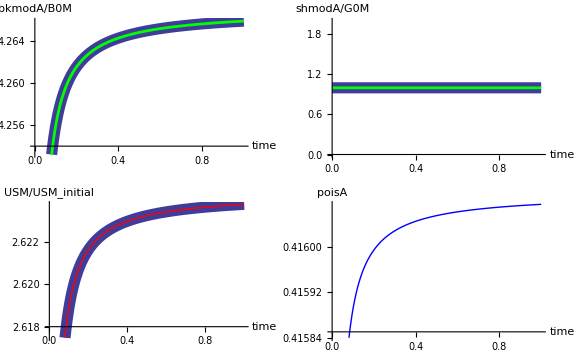

```mathematica
octo[scaler,Max[I1]];octo[scaler,Min[I1]]
```

```mathematica
npic=50;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
showme[LodeXsig,LodeYsig]
```

```mathematica
showme[LODE]
```

TTTproblem: Why do these plots show octahedral motion, but stressSpace[] does not. 
Is it the scale of this problem which involves ridiculously massive pressures (600 times larger than shear stress)?

```mathematica
showmeAll[sigm/B0M,sigs/B0M]
```

## Closer Look

```mathematica
{J3TYPEM,A1M,A2M,A3M,A4M}
{RKM,RK0}
I1min=Min[I1]
I1max=Max[I1]
Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,I1barmin,I1barmax}]
showme[Table[RKfnt[RKM,I1[[i]],A2M,A3M,A4M],{i,lastep}]]
```

```mathematica
showme[LODE]
showme[sigs]
```

```mathematica
showcy[eps11]
```

```mathematica
showcy[eps22]
```

```mathematica
showcy[eps33]
```

## stress-strain paths

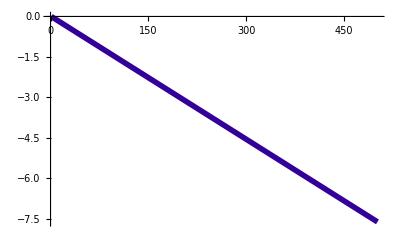

```mathematica
showcy[vstrain]
```

```mathematica
If[geocrack,showme[COHER]]
```

# ORTHO Isotropic compression

The following line tells Mathematica which directory to use when looking for the data. This input set is for the isotropic (ii) simulation, so we set runid equal to "I". Then next line constructs the location that Mathematica will look for the data files.

## Overview

```mathematica
setRun["kayenta-ortho-isotropic-compression"]
```

TTTconcern: Why is there ANY nonzero value for J2, even though small.

At this point, all field variables are available for plotting. If you can't remember a plot variable keyword, just look at the ".out" file. You can also define derived variables. For example, below we define the the volumetric strain to equal the trace of the strain:

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[]
```

```mathematica
npic=2;incstep=Max[IntegerPart[lastep/npic],1];Do[OCTO1[istep],{istep,1,lastep,incstep}]
```

```mathematica
showcy[I1/P0M]
```

```mathematica
xright=Max[I1/P0M];CrushCurve=Plot[P3M E^(-(P1M+P2M (-x P0M+P0M))((-x P0M+P0M))),{x,0,xright}, PlotRange->{0,P3U},PlotStyle->ExactStyle]
```

```mathematica
showme[-EQPV]
```

```mathematica
CrushCalc=showme[I1/P0M,P3M+EQPV];Show[CrushCurve,CrushCalc]
```

## Look at results in detail

```mathematica
showme[-EQPV,PRES*3]
```

```mathematica
showme[-vstrain,PRES]
```

```mathematica
bkmodU=B0U+B1U
```

```mathematica
showme[-vstrain-PRES/bkmodU,PRES]
```

```mathematica
showcy[rho]
```

```mathematica
showcy[PRES+I1/3]
```

```mathematica
showme[-vstrain,PRES/B0U,{"volumetric strain","normalized pressure"}];
```

```mathematica
showme[timestep]
```

```mathematica
{CTI1U,CTPSU}
```

```mathematica
{B0U,B1U,B2U,B3U,B4U}
```

```mathematica
showme[vstrain,I1/CTI1U]
```

```mathematica
showme[time,I1/4.5*^10]
```

```mathematica
showme[time,HK]
```

```mathematica
showme[eps11+eps22+eps33]
showme[vstrain,I1]
```

```mathematica
showme[EQPV]
```

```mathematica
showme[vstrain,QSSIGZZ]
```

```mathematica
Show[showme[vstrain,sig11],showme[vstrain,sig22],showme[vstrain,sig33]]
```

```mathematica
showme[-vstrain,-(sig11-sig22)]
```

```mathematica
showme[-vstrain,-(sig22-sig33)]
```

```mathematica
showme[-vstrain,-(sig33-sig11)]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Drucker-Prager **

## Overview

### Overview (minimal)

```mathematica
setRun["kayenta-drucker-prager"]
```

### Overview continued

```mathematica
meridianALLbasic[5,scaler]
 meridianALL[5,scaler]
reportGraphic["pmerid.gif",%]
elasticInfo[]
```

```mathematica
showme[YIELD]
```

```mathematica
xport["DPmeridtest.gif",meridtest]
```

```mathematica
CTPSM
```

```mathematica
showme[time,sigs]
```

```mathematica
RKM
```

```mathematica
showme[time,sigm]
```

```mathematica
showme[BACKRN]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1]
Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
{CTI1U,CTI1M}/Sqrt[3]
```

## comparison with Exact Analytical result

The EXACT Analytical solution for this problem is solved in the Mathematica notebook /home/rmbrann/docs/Verification/Axisymmetric.nb
The solution is discussed in FrameMaker file 
These are the results...

```mathematica
PWLtime={0,1,3/2,2,5/2,3,10/3,(5 (-22+7 √6))/(12 (-3+√6)),4,5};
```

```mathematica
PWLsigA={0,-850/3,-50/3 (9+4 √6),-50/3 (9+4 √6),50/3 (-3+2 √6),-110+160 √(2/3),-110+160 √(2/3),50,50,(-118 √2+292 √3)/(3 √2+2 √3)};pwlsigA=interp[PWLtime,PWLsigA];PWLsigL={0,-850/3,50/3 (-9+2 √6),50/3 (-9+2 √6),-50/3 (3+√6),-10/3 (33+8 √6),(10 (-49 √2+58 √3))/(3 √2+2 √3),50,50,(-58 √2+64 √3)/(3 √2+2 √3)};pwlsigL=interp[PWLtime,PWLsigL];
```

```mathematica
PWLz={0,-850/(√3),-150 √3,-150 √3,-50 √3,-110 √3,(1260-330 √6)/(3 √2+2 √3),50 √3,50 √3,(420-78 √6)/(3 √2+2 √3)};pwlz=interp[PWLtime,PWLz];
PWLr={0,0,200,200,-100,-160,-(160 √2 (-3+√6))/(3 √2+2 √3),0,0,(228 √2-40 √3)/(3 √2+2 √3)};pwlr=interp[PWLtime,PWLr];
```

```mathematica
PWLepsA={0,-17/1800,(-9-16 √6)/1800,(-1-32 √6)/1800,(5-8 √6)/1800,(11+16 √6)/1800,(645 √2+14 √3)/(9000 (3 √2+2 √3)),(-89+32 √6)/9000,(645 √2-1138 √3)/(9000 (3 √2+2 √3)),(525 √2-682 √3)/(9000 (3 √2+2 √3))};pwlepsA=interp[PWLtime,PWLepsA];
PWLepsL={0,-17/1800,(-9+8 √6)/1800,(-1+16 √6)/1800,(5+4 √6)/1800,(11-8 √6)/1800,(-75 √2+446 √3)/(9000 (3 √2+2 √3)),(199+8 √6)/9000,(-75 √2+1598 √3)/(9000 (3 √2+2 √3)),(-3 √2+274 √3)/(1800 (3 √2+2 √3))};pwlepsL=interp[PWLtime,PWLepsL];
```

The following illustrates how to make interpolating functions for the model results that can be compared with the interpolation functions that were made above for the PWL exact results.

```mathematica
mdlepsA=interp[time,eps11];
mdlepsL=interp[time,eps22];
mdlsigA=interp[time,sig11];
mdlsigL=interp[time,sig22];
mdlz=interp[time,sigm];
mdlr=interp[time,sigs];
```

```mathematica
tmax=Max[time]
```

```mathematica
Plot[mdlepsA[t],{t,0,tmax}]
```

```mathematica
Plot[pwlepsA[t],{t,0,tmax}]
```

```mathematica
Plot[mdlepsA[t]-pwlepsA[t],{t,0,tmax}]
```

The following uses the pre-built function "compare" (defined in the once-only section) to generate viewgraph metric plots.
The error is the point-wise L2 norm.

Note: The model driver is failing to reproduce the prescribed strains exactly (about half a percent error).
I need to find the source of this problem. The driving strain should be exact.

```mathematica
DPtimeepsA=compare[PWLtime,PWLepsA,time,eps11,"axial strain"]
DPtimeepsL=compare[PWLtime,PWLepsL,time,eps33,"lateral strain"]
DPtimesigA=compare[PWLtime,PWLsigA,time,sig11,"axial stress"]
DPtimesigL=compare[PWLtime,PWLsigL,time,sig22,"lateral stress"]
DPepsDsigD=compare[PWLepsA-PWLepsL,PWLsigA-PWLsigL,eps11-eps22,sig11-sig22]
DPepsVsigM=compare[PWLepsA+2PWLepsL,(PWLsigA+2PWLsigL)/3,eps11+2eps22,(sig11+2sig22)/3]
reportGraphic["pvolstressVSstrain.gif",%]
```

```mathematica
(*xxx=".gif";resolution=100;
Export["DPtimeepsA"<>xxx,DPtimeepsA,ImageResolution->resolution]
Export["DPtimeepsL"<>xxx,DPtimeepsL,ImageResolution->resolution]
Export["DPtimesigA"<>xxx,DPtimesigA,ImageResolution->resolution]
Export["DPtimesigL"<>xxx,DPtimesigL,ImageResolution->resolution]
Export["DPepsDsigD"<>xxx,DPepsDsigD,ImageResolution->resolution]
Export["DPepsVsigM"<>xxx,DPepsVsigM,ImageResolution->resolution]*)
```

```mathematica
cmpr[PWLtime,PWLepsA,time,eps11,"axial strain"]
cmpr[PWLtime,PWLepsL,time,eps22,"lateral strain"]
cmpr[PWLtime,PWLsigA,time,sig11,"axial stress"]
cmpr[PWLtime,PWLsigL,time,sig22,"lateral stress"]
```

```mathematica
Show[ListPlot[maketab[PWLtime,PWLepsA],Joined->True,PlotStyle->{Thickness[0.01],RGBColor[1,0,0]}],ListPlot[maketab[PWLtime,PWLepsL],Joined->True,PlotStyle->{Thickness[0.01],RGBColor[0,0,1],Dashing[{0.05,0.05}]}]]
```

```mathematica
(*Export["DPstrains.jpg",%,ImageResolution->300]*)
```

```mathematica
N[{PWLtime[[1]],PWLtime[[2]],PWLtime[[4]],PWLtime[[6]],PWLtime[[9]]},12]
N[{PWLepsA[[1]],PWLepsA[[2]],PWLepsA[[4]],PWLepsA[[6]],PWLepsA[[9]]},12]
N[{PWLepsL[[1]],PWLepsL[[2]],PWLepsL[[4]],PWLepsL[[6]],PWLepsL[[9]]},12]
```

```mathematica
PWLtime
PWLepsA
PWLepsL
PWLsigA
PWLsigL
```

```mathematica
PWLsigL//TableForm
```

```mathematica
{CTPSU,CTPSM,CTI1U,CTI1M}
```

```mathematica
showme[DCSP]
```

TTTobservation: DCSP is different, but I think that's because I now normalize the normal and flow direction

```mathematica
If[geocrack,showme[COHER]]
```

# Constant spin in PI-plane

## Overview

```mathematica
setRun["kayenta-pispin"]
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[]
```

```mathematica
p1=showme[time,eps11,{"time","e11"}]
p2=showme[time,eps11,{"time","e22"}]
p3=showme[time,eps11,{"time","e33"}]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

## Closer Look

```mathematica
showcy[PRES]
```

```mathematica
Show[showcy[sigs/(Sqrt[2](A1M-A3M))],showcy[sigd22]]
```

## Pi plane spin is defined so that Lode angle will increase linearly in time

This is a plot of y=x for later use.

```mathematica
straight=Plot[x,{x,-0.015,0.005},PlotStyle->{red,chainDash}]
```

```mathematica
stressZEROyslope=showme[eps11,sig11/(2. G0M)]
```

```mathematica
stressZEROyslope=showme[eps11,QSSIGXX/(2. G0M)]
```

During the initial elastic loading, the demo program is expected to predict that sig11=2G eps11. The following plot verifies that the demo program is getting this behavior correctly. In the plot below, the dashed straight line shows the expected initial elastic response (stress equals strain times twice the shear modulus).

```mathematica
Show[stressZEROyslope,straight,AxesLabel->{"eps11","sig11"}]
```

```mathematica
stressZEROyslope=ListPlot[Table[{eps11⟦i⟧,sig11⟦i⟧/(2. G0M)},{i,1,lastep}],Joined->True,PlotStyle->{blue,chainDash}]
```

```mathematica
showme[time,LODE,{"time","LODE"}]
```

```mathematica
Show[showme[sigs/(Sqrt[2]*A1M)-1],AxesLabel->{"time","r/R -1"}]
```

```mathematica
showme[eps11+eps22+eps33]
```

```mathematica
showme[EQDOT]
```

```mathematica
showhis[EQPS]
```

```mathematica
showhis[SHEAR]
```

```mathematica
showme[ROOTJ2/A1M]
```

```mathematica
lastep
```

```mathematica
If[geocrack,showme[COHER]]
```

# Sandler-Rubin-Pucik **

This is the "contrived" SRP test where the yield surface has a slope exactly 1 in stress space.
The analytical solution is worked out in

## Overview

```mathematica
setRun["kayenta-sandler-rubin"]
```

```mathematica
{{A1U,A2U,A3U,A4U},{A1M,A2M,A3M,A4M}}//MatrixForm
```

```mathematica
{{A1U,A2PFU,A3U,A4PFU},{A1M,A2PFM,A3M,A4PFM}}//MatrixForm
```

```mathematica
meridianALLbasic[2,scaler]; meridianALL[1,scaler];elasticInfo[];
```

```mathematica
meridianALL[1,1]
```

```mathematica
(*Export["SRPmeridtest.jpg",meridtest,ImageResolution->300]*)
```

```mathematica
Show[meridtest]
```

## comparison with Exact Analytical result

The Exact Analytical solution for this problem is solved in the Mathematica notebook called UniaxialAnalytical.nb.
These are the results...

```mathematica
PWLtime={0,1,3/2,2,3,4};
```

```mathematica
PWLsigA={0,-200 √3,-(200 (3+4 √2))/(√3),-(200 (3+4 √2))/(√3),-200 √(2/3),(200 (-9+2 √2))/(√3)};pwlsigA=interp[PWLtime,PWLsigA];PWLsigL={0,-200 √3,(200 (-3+2 √2))/(√3),(200 (-3+2 √2))/(√3),100 √(2/3),-200 √(2/3)};pwlsigL=interp[PWLtime,PWLsigL];
```

```mathematica
PWLepsA={0,-1/(200 √3),-(3+16 √2)/(600 √3),-(3+32 √2)/(600 √3),1/450 (6 √3-11 √6),-(3+32 √2)/(600 √3)};pwlepsA=interp[PWLtime,PWLepsA];
PWLepsL={0,-1/(200 √3),(-3+8 √2)/(600 √3),(-3+16 √2)/(600 √3),(-6+11 √2)/(300 √3),(-3+16 √2)/(600 √3)};pwlepsL=interp[PWLtime,PWLepsL];
```

The following illustrates how to make interpolating functions for the model results that can be compared with the interpolation functions that were made above for the PWL exact results.

```mathematica
mdlepsA=interp[time,eps11];
mdlepsL=interp[time,eps22];
mdlsigA=interp[time,sig11];
mdlsigL=interp[time,sig22];
```

```mathematica
tmax=Max[time]
```

```mathematica
Plot[mdlepsA[t],{t,0,tmax}]
```

```mathematica
Plot[pwlepsA[t],{t,0,tmax}]
```

```mathematica
Plot[mdlepsA[t]-pwlepsA[t],{t,0,tmax}]
```

The following uses the pre-built function "compare" (defined in the once-only section) to generate viewgraph metric plots.
The error is the point-wise L2 norm.

```mathematica
compare[PWLtime,PWLepsA,time,eps11,"axial strain"]
```

```mathematica
SRPtimeepsA=compare[PWLtime,PWLepsA,time,eps11,"axial strain"]
SRPtimeepsL=compare[PWLtime,PWLepsL,time,eps22,"lateral strain"]
SRPtimesigA=compare[PWLtime,PWLsigA,time,sig11,"axial stress"]
SRPtimesigL=compare[PWLtime,PWLsigL,time,sig22,"lateral stress"]
SRPepsDsigD=compare[(PWLepsA-PWLepsL),(PWLsigA-PWLsigL),(eps11-eps22),(sig11-sig22)];
SRPepsVsigM=compare[PWLepsA+2PWLepsL,(PWLsigA+2PWLsigL)/3,eps11+2eps22,(sig11+2sig22)/3];
```

```mathematica
(*Export["SRPtimeepsA.jpg",SRPtimeepsA,ImageResolution->300]
Export["SRPtimeepsL.jpg",SRPtimeepsL,ImageResolution->300]
Export["SRPtimesigA.jpg",SRPtimesigA,ImageResolution->300]
Export["SRPtimesigL.jpg",SRPtimesigL,ImageResolution->300]
Export["SRPepsDsigD.jpg",SRPepsDsigD,ImageResolution->300]
Export["SRPepsVsigM.jpg",SRPepsVsigM,ImageResolution->300]*)
```

```mathematica
makeme[PWLtime,PWLepsA]
```

```mathematica
?Dashing
```

```mathematica
as
```

```mathematica
Show[ListPlot[maketab[PWLtime,PWLepsA],Joined->True,PlotStyle->{Thickness[0.01],RGBColor[1,0,0]}],ListPlot[maketab[PWLtime,PWLepsL],Joined->True,PlotStyle->{Thickness[0.01],RGBColor[0,0,1],Dashing[{0.05,0.03}]}]]
```

```mathematica
(*Export["SRPstrains.jpg",%,ImageResolution->300]*)
```

```mathematica
PWLtime
PWLepsA
PWLepsL
PWLsigA
PWLsigL
```

```mathematica
Simplify[PWLepsL]
N[PWLepsL]
```

```mathematica
workrate=sig11 d11+2(sig22 d22);
```

```mathematica
showme[time,workrate]
```

```mathematica
(*Export["SRPworkrate.jpg",%,ImageResolution->300]*)
```

```mathematica
Length[workrate]
```

```mathematica
lastep
```

```mathematica
showcy[workrate]
```

```mathematica
showcy[workrate]
```

```mathematica
showcy[sig11]
```

```mathematica
showcy[sig22]
```

```mathematica
showme[d11]
```

Make a data pair array of time vs. workrate for the last two strain legs.

```mathematica
lastep
Length[workrate]
Length[time]
{i,1250/2,lastep}
```

```mathematica
wrkrate=Table[{time[[i]],workrate[[i]]},{i,lastep}];
```

```mathematica
Dimensions[wrkrate]
```

```mathematica
ListPlot[wrkrate]
```

```mathematica
(*<<NumericalMath`ListIntegrate`*)
```

The last two strain legs constitute a closed strain cycle of the type discussed by Sandler, Rubin, and Pucik, who show that such cycles entail negative net work and therefore imply that energy can be extracted from the system. The following numerical integration verifies this claim numerically.

```mathematica
K=B0M;G=G0M;fac1=1/(2G);fac2=(1/(3K)-1/(2G))/3;epsEA=fac1 sig11+fac2 I1;epsEL=fac1 sig22+fac2 I1;epsPA=eps11-epsEA;epsPL=eps22-epsEL;
```

```mathematica
showme[time,-eps11]
showme[time,-epsEA]
showme[time,-epsPA]
```

```mathematica
showme[time,-eps22]
showme[time,-epsEL]
showme[time,-epsPL]
```

```mathematica
showme[time,-(eps11-eps22)]
showme[time,-(epsEA-epsEL)]
showme[time,-(epsPA-epsPL)]
```

```mathematica
epsEAi=Interpolation[maketab[time,epsEA]]
epsELi=Interpolation[maketab[time,epsEL]]
epsPAi=Interpolation[maketab[time,epsPA]]
epsPLi=Interpolation[maketab[time,epsPL]]
```

```mathematica
Show[showme[time,epsPA],Plot[epsPAi[x],{x,0,4}]]
```

```mathematica
epsEAdot=epsEAi'[x]
```

```mathematica
epsEAdot[.5]
```

```mathematica
pltE=Plot[Sqrt[epsEAi'[x]^2+2(epsELi'[x]^2)],{x,0,4},PlotStyle->{RGBColor[1,0,0]}]
```

```mathematica
pltP=Plot[Sqrt[epsPAi'[x]^2+2(epsPLi'[x]^2)],{x,0,4},PlotStyle->{RGBColor[0,0,1]}]
```

```mathematica
pltE=Plot[epsEAi'[x] epsPAi'[x]+2(epsELi'[x] epsPLi'[x]),{x,0,4},PlotStyle->{RGBColor[1,0,0]},PlotRange->All]
```

```mathematica
Show[pltE,pltP,PlotRange->All]
```

```mathematica
(*Export["magstnrates.jpg",%]*)
```

```mathematica
?maketab
```

```mathematica
jnk=Table[√(d11⟦i⟧^2+2 d22⟦i⟧^2),{i,1,lastep}];Show[showme[time,jnk],pltE,pltP]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Sandler-Rubin-Pucik with linear hardening **

This input set is used for SRP tests that have more realistic material parameters. 
Kayenta inputs and analytical results are worked out in  /home/rmbrann/docs/Verification/SandlerRubinPucik/SandlerRubinAnalytical.nb

## Overview

```mathematica
setRun["kayenta-sandler-rubin-w-hardening"]
```

```mathematica
{{A1U,A2U,A3U,A4U},{A1M,A2M,A3M,A4M}}//MatrixForm
```

```mathematica
{{A1U,A2PFU,A3U,A4PFU},{A1M,A2PFM,A3M,A4PFM}}//MatrixForm
```

```mathematica
meridianALLbasic[2,scaler]; meridianALL[1,scaler];elasticInfo[];
```

```mathematica
meridianALL[1,1]
```

```mathematica
{A2M,A4M,CRM,RKM}
{A2PFM,A4PFM,CRPFM,RKPFM}
```

```mathematica
(*Export["SRPmeridtest.jpg",meridtest,ImageResolution->100]*)
```

```mathematica
Show[meridtest]
```

## comparison with Exact Analytical result

The Exact Analytical solution for this problem is solved in the Mathematica notebook called UniaxialAnalytical.nb.
These are the results...

```mathematica
PWLtime={0,1,2,3,4};
```

The old governing equations implemented kinematic hardening as an internal variable variable in a classical way.
The new governing equations implement kinematic hardening as a stress transform that alters the origin for elastic response (thus allowing kinematic hardening to translate the yield surface so much that the origin in stress space can eventually become outside the yield surface (which, believe it or not, has actually been seen in laboratory data).  

There is very little difference between the old and new formulations. Below, you should select which analytical solution you wish to compare against. Select "old" if running with the old GeoModel. Select "new" if running with Brannon's new Kayenta framework.

```mathematica
analyticalSolution=new;
```

```mathematica
Switch[analyticalSolution,

old,
PWLsigA={0,-115.47005383792515290,-1788.0862739787473096,-456.58193875019501187,-1402.7723254312014346};PWLsigL={0,-115.47005383792515290,-115.47005383792515290,113.78201514944334125,-308.12702811169809041};
PWLepsA={0,-0.00009622504486,-0.004277765595,-0.002615471367,-0.004277765595};
PWLepsL={0,-0.00009622504486,0.001297621805,0.001212311555,0.001297621805};,

new,
PWLsigA={0,-115.47005383792515290,-1788.0862739787473096,-487.40705463399868187,-1433.5974413150051046};
PWLsigL={0,-115.47005383792515290,-115.47005383792515290,129.19457309134517625,-292.71447016979625541};
PWLepsA={0,-0.00009622504486,-0.004277765595,-0.002615471367,-0.004277765595};
PWLepsL={0,-0.00009622504486,0.001297621805,0.001212311555,0.001297621805};]
```

```mathematica
pwlsigA=interp[PWLtime,PWLsigA];pwlsigL=interp[PWLtime,PWLsigL];
pwlepsA=interp[PWLtime,PWLepsA];pwlepsL=interp[PWLtime,PWLepsL];
```

The following illustrates how to make interpolating functions for the model results that can be compared with the interpolation functions that were made above for the PWL exact results.

```mathematica
mdlepsA=interp[time,eps11];
mdlepsL=interp[time,eps22];
mdlsigA=interp[time,sig11];
mdlsigL=interp[time,sig22];
```

```mathematica
tmax=Max[time]
```

```mathematica
Plot[mdlepsA[t],{t,0,tmax}]
```

```mathematica
Plot[pwlepsA[t],{t,0,tmax}]
```

```mathematica
Plot[mdlepsA[t]-pwlepsA[t],{t,0,tmax}]
```

The following uses the pre-built function "compare" (defined in the once-only section) to generate viewgraph metric plots.
The error is the point-wise L2 norm.


NOTE: Using the default Kayenta hardening will produce errors starting at time=2 because the default hardening is nonlinear whereas the exact solution is for linear hardening.

Getting an exact match requires running the special version of Kayenta that has special code to allow linear hardening.

```mathematica
SRPtimeepsA=compare[PWLtime,PWLepsA,time,eps11,"axial strain"]
SRPtimeepsL=compare[PWLtime,PWLepsL,time,eps22,"lateral strain"]
SRPtimesigA=compare[PWLtime,PWLsigA,time,sig11,"axial stress"]
SRPtimesigL=compare[PWLtime,PWLsigL,time,sig22,"lateral stress"]
SRPepsDsigD=compare[-(PWLepsA-PWLepsL),-(PWLsigA-PWLsigL),-(eps11-eps22),-(sig11-sig22)]
SRPepsVsigM=compare[-(PWLepsA+2PWLepsL),-(PWLsigA+2PWLsigL)/3,-(eps11+2eps22),-(sig11+2sig22)/3]
```

COMMENT: The last two plots show, respectively,
	stress difference vs strain difference
and 
	pressure vs. volumetric strain .
	
For plastic incompressibility, the volumetric response is the elastic volumetric response (thus the straight line).


The stress/strain difference plot is VERY interesting. 

Leg 1 contributes nothing to the stress/strain diff plot. The first response is the elastic triaxial loading of Leg 2. The middle part, which looks like an unloading, is actually the plastic loading of Leg 3. The final part is the elastic reloading of the SRP cycle.

```mathematica
(*Export["SRPtimeepsA.jpg",SRPtimeepsA,ImageResolution->100]
Export["SRPtimeepsL.jpg",SRPtimeepsL,ImageResolution->100]
Export["SRPtimesigA.jpg",SRPtimesigA,ImageResolution->100]
Export["SRPtimesigL.jpg",SRPtimesigL,ImageResolution->100]
Export["SRPepsDsigD.jpg",SRPepsDsigD,ImageResolution->100]
Export["SRPepsVsigM.jpg",SRPepsVsigM,ImageResolution->100]*)
```

```mathematica
Show[ListPlot[maketab[PWLtime,PWLepsA],Joined->True,PlotStyle->{Thickness[0.01],RGBColor[1,0,0]}],ListPlot[maketab[PWLtime,PWLepsL],Joined->True,PlotStyle->{Thickness[0.01],RGBColor[0,0,1],Dashing[{0.05,0.03}]}]]
```

```mathematica
(*Export["SRPstrains.jpg",%,ImageResolution->100]*)
```

```mathematica
PWLtime
PWLepsA
PWLepsL
PWLsigA
PWLsigL
```

```mathematica
Simplify[PWLepsL]
N[PWLepsL]
```

```mathematica
workrate=sig11 d11+2(sig22 d22);
```

```mathematica
showme[time,workrate];
```

```mathematica
(*Export["SRPworkrate.jpg",%,ImageResolution->100]*)
```

```mathematica
showcy[workrate]
```

```mathematica
cyc=201
showcy[workrate,201,lastep-1];
```

```mathematica
(*showcy[TWORKRATE,cyc,lastep];*)
```

```mathematica
showme[d11]
```

Make a data pair array of time vs. workrate for the last two strain legs.

```mathematica
wrkrate=Table[{time[[i]],workrate[[i]]},{i,cyc,lastep}];
```

```mathematica
ListPlot[wrkrate]
```

```mathematica
(*<<NumericalMath`ListIntegrate`*)
```

```mathematica
∫_1^Length[wrkrate] Interpolation[wrkrate,InterpolationOrder->2][N]ⅆN
```

The last two strain legs constitute a closed strain cycle of the type discussed by Sandler, Rubin, and Pucik, who show that such cycles entail negative net work and therefore imply that energy can be extracted from the system. The following numerical integration verifies this claim numerically.

```mathematica
showme[INDEX]
```

```mathematica
K=B0M;G=G0M;fac1=1/(2G);fac2=(1/(3K)-1/(2G))/3;
epsEA=fac1 sig11+fac2 I1;
epsEL=fac1 sig22+fac2 I1;
epsPA=eps11-epsEA;epsPL=eps22-epsEL;
```

```mathematica
showme[time,-eps11];
showme[time,-epsEA];
showme[time,-epsPA];
```

```mathematica
showme[time,-eps22];
showme[time,-epsEL];
showme[time,-epsPL];
```

```mathematica
showme[time,-(eps11-eps22)];
showme[time,-(epsEA-epsEL)];
showme[time,-(epsPA-epsPL)];
```

```mathematica
epsEAi=Interpolation[maketab[time,epsEA]];
epsELi=Interpolation[maketab[time,epsEL]];
epsPAi=Interpolation[maketab[time,epsPA]];
epsPLi=Interpolation[maketab[time,epsPL]];
```

```mathematica
Show[showme[time,epsPA],Plot[epsPAi[x],{x,0,4}]]
```

```mathematica
epsEAdot=epsEAi'[x]
```

```mathematica
epsEAdot[.5]
```

```mathematica
pltE=Plot[Sqrt[epsEAi'[x]^2+2(epsELi'[x]^2)],{x,0,4},PlotStyle->{RGBColor[1,0,0]}]
```

```mathematica
pltP=Plot[Sqrt[epsPAi'[x]^2+2(epsPLi'[x]^2)],{x,0,4},PlotStyle->{RGBColor[0,0,1]},PlotRange->All]
```

```mathematica
pltE=Plot[epsEAi'[x] epsPAi'[x]+2(epsELi'[x] epsPLi'[x]),{x,0,4},PlotStyle->{RGBColor[1,0,0]},PlotRange->All]
```

```mathematica
Show[pltE,pltP]
```

```mathematica
(*Export["magstnrates.jpg",%]*)
```

```mathematica
?maketab
```

```mathematica
jnk=Table[√(d11⟦i⟧^2+2 d22⟦i⟧^2),{i,1,lastep}];Show[showme[time,jnk],pltE,pltP]
```

```mathematica
(*showcy[workrate-TWORKRATE]*)
```

```mathematica
If[geocrack,showme[COHER]]
```

# Pure shear strain nonhardening with rate dependence

```mathematica
demodir
```

## Overview

```mathematica
setRun["kayenta-pure-shear-w-rate-dep"]
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

## Simple deviatoric "shear" strain ... more plots

```mathematica
{A1U,A3U,RNU,B0U,G0U}
```

```mathematica
yldINshear=(A1U-A3U)
```

```mathematica
sig11yld=yldINshear
eps11yld=sig11yld/(2 G0U)
```

```mathematica
showme[Sqrt[3/4]Abs[sig11]-ROOTJ2]
```

```mathematica
Max[ROOTJ2]/yldINshear
```

```mathematica
Max[sig11]/sig11yld
```

```mathematica
showme[time,sig11,{"time","stress11"}]
```

```mathematica
showme[ROOTJ2 /yldINshear]
showme[sig11/sig11yld]
```

```mathematica
straight=Plot[x,{x,-1,1},PlotStyle->{red,chainDash}]
```

```mathematica
straight=Plot[{x,1,-1},{x,-1,1},PlotStyle->{{red,chainDash}}]
```

The following plot shows sig11/(2G) versus eps11, where G is the shear modulus. The strain path is purely deviatoric. Therefore, since yslope and hardmod were given in "demo.inp" to be zero, the demo program should predict a result that looks like classical nonhardening plasticity.

```mathematica
stressZEROyslope=showme[eps11/eps11yld,sig11/sig11yld]
```

```mathematica
showme[sig11]
```

```mathematica
showme[sig22]
```

During the initial elastic loading, the demo program is expected to predict that sig11=2G eps11. The following plot verifies that the demo program is getting this behavior correctly. In the plot below, the dashed straight line shows the expected initial elastic response (stress equals strain times twice the shear modulus).

```mathematica
?med*
```

```mathematica
straight=ListPlot[Table[{eps11⟦i⟧/eps11yld,QSSIGXX⟦i⟧/sig11yld},{i,1,lastep}],Joined->True,PlotStyle->{red,chainDash,medLine}];
```

```mathematica
Show[stressZEROyslope,straight,AxesLabel->{"strain/epsY","stress/(<sigY>)"}]
```

```mathematica
If[MakeGraphs,Export[demodir<>"sRATE.gif",%]]
```

```mathematica
Show[makeme[eps11/eps11yld,QSSIGXX/sig11yld],straight]
```

```mathematica
showme[QSSIGXX,sig11]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Pure shear strain with linear hardening **

## Overview

```mathematica
setRun["kayenta-pure-shear-w-lin-hardening"]
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

## Simple deviatoric "shear" strain ... more plots

```mathematica
showme[ROOTJ2 /A1M];
showme[sig11/A1M];
```

The following is the analytical solution

```mathematica
A1M
```

```mathematica
IntegerPart[A1M]
```

```mathematica
sstar=Rationalize[0.2];a1=Rationalize[A1M-RNM];
tref=Rationalize[sstar/d11⟦2⟧];
elasticTangentMod=Rationalize[2 G0M];
hc=Rationalize[Abs[HCM]];
plasticTangentMod=2 G0M (1-1/(1+hc/(2 G0M)));
plasticTangentMod=hc;
strainRate=Rationalize[d11⟦1⟧];
strainRef=strainRate tref;
strain0A=strainRate t;
stress0A=elasticTangentMod strain0A;
stressA=a1;
tA=t/.Solve[stress0A==stressA,t]⟦1⟧;
strainA=strain0A/.t->tA;
eqps0A=0;
eqpsA=0;
strainA1=strainRate t;
stressA1=stressA+plasticTangentMod (strainA1-strainA);
stress1=stressA1/.t->tref;
eqpsA1=eqpsA+strainRate (t-tA);
eqps1=eqpsA1/.t->tref;
strain1B=strainRef-strainRate (t-tref);
stress1B=stress1+elasticTangentMod (strain1B-strainRef);
stressB=stress1-2 a1;
tB=t/.Solve[stress1B==stressB,t]⟦1⟧;
strainB=strain1B/.t->tB;
eqps1B=eqps1;
eqpsB=eqps1;
strainB3=strainRef-strainRate (t-tref);
stressB3=stressB+plasticTangentMod (strainB3-strainB);
stress3=stressB3/.t->3 tref;
strain3=-strainRef;
eqpsB3=eqpsB+strainRate (t-tB);
eqps3=eqpsB3/.t->3 tref;
strain3C=strainRate (t-4 tref);
stress3C=stress3+elasticTangentMod (strain3C-strain3);
stressC=stress3+2 a1;
tC=t/.Solve[stress3C==stressC,t]⟦1⟧;
strainC=strain3C/.t->tC;
eqps3C=eqps3;
eqpsC=eqps3;
strainC4=strainRate (t-4 tref);
stressC4=stressC+plasticTangentMod (strainC4-strainC);
stress4=stressC4/.t->4 tref;
eqpsC4=eqpsC+strainRate (t-tC);
eqps4=eqpsC4/.t->4 tref;
stressHistory=Simplify[Piecewise[{{stress0A, 0≤t<tA}, {stressA1, tA≤t<tref}, {stress1B, tref≤t<tB}, {stressB3, tB≤t<3 tref}, {stress3C, 3 tref≤t<tC}, {stressC4, tC≤t≤4 tref}}]];
sig11EXACT=Table[stressHistory/.t->time⟦i⟧,{i,lastep}];
eqpsHistory=Simplify[2 (Piecewise[{{eqps0A, 0≤t<tA}, {eqpsA1, tA≤t<tref}, {eqps1B, tref≤t<tB}, {eqpsB3, tB≤t<3 tref}, {eqps3C, 3 tref≤t<tC}, {eqpsC4, tC≤t≤4 tref}}])];
eqpsEXACT=Table[eqpsHistory/.t->time⟦i⟧,{i,lastep}];
Plot[stressHistory,{t,0,4 tref}]
Plot[eqpsHistory,{t,0,4 tref}]
```

Note: The legacy GeoModel does not support true linear hardening. It progressively decreases hardening to a saturation point (controlled by user input RN and, internally, via GFUN). The new framework will support linear hardening if the hardening modulus is input as a negative number.

```mathematica
compare[time,eqpsEXACT,time,EQPS]
```

```mathematica
compare[eps11/strainA,sig11EXACT/A1M,eps11/strainA,(sig11)/A1M]
reportGraphic["sLinearHardening.gif",%]
```

```mathematica
compare[time,sig11EXACT/A1M,time,(sig11)/A1M]
```

```mathematica
(*Export[ToFileName[demodir,"LinearHardeningSig11vsTime.gif"],%]*)
```

```mathematica
err=(sig11-sig11EXACT)/A1M;
showme[err]
{Min[err],Max[err]}
```

```mathematica
showmeAll[time, GFUN]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Isochoric triaxial strain

## Overview

```mathematica
setRun["kayenta-isochoric-triax-strain"]
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[OCTO1[istep],{istep,1,lastep,incstep}]
```

## Simple deviatoric "shear" strain ... more plots

This is a plot of y=x for later use.

```mathematica
{A1U,A3U,RNU}
```

```mathematica
yldINshear=(A1M-A3M)
```

```mathematica
sig11yld=yldINshear/Sqrt[3/4]
eps11yld=sig11yld/(2 G0U)
```

```mathematica
showme[Sqrt[3/4]Abs[sig11]-ROOTJ2]
```

```mathematica
Max[ROOTJ2]/yldINshear
```

```mathematica
Max[sig11]/sig11yld
```

```mathematica
showme[ROOTJ2 /yldINshear];
showme[sig11/sig11yld];
```

```mathematica
straight=Plot[{x,1,-1},{x,-1,1},PlotStyle->{{red,chainDash}}];
```

The following plot shows sig11/(2G) versus eps11, where G is the shear modulus. The strain path is purely deviatoric. Therefore, since yslope and hardmod were given in "demo.inp" to be zero, the demo program should predict a result that looks like classical nonhardening plasticity.

```mathematica
stressZEROyslope=showme[eps11/eps11yld,sig11/sig11yld]
```

```mathematica
stressZEROyslope=ListPlot[Table[{eps11⟦i⟧/eps11yld,sig11⟦i⟧/sig11yld},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01]}]
```

During the initial elastic loading, the demo program is expected to predict that sig11=2G eps11. The following plot verifies that the demo program is getting this behavior correctly. In the plot below, the dashed straight line shows the expected initial elastic response (stress equals strain times twice the shear modulus).

```mathematica
straight=ListPlot[Table[{eps11⟦i⟧/eps11yld,QSSIGXX⟦i⟧/sig11yld},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01],red,chainDash}];
```

```mathematica
Show[straight,stressZEROyslope,PlotRange->All]
```

```mathematica
If[geocrack,showme[COHER]]
```

# (u) Uniaxial strain (geocrack)

TTTcomment: This works fine when cap is suppressed.

Uniaxial strain is a good test for the any yield model because it is neither purely isotropic nor purely deviatoric.

## Overview

```mathematica
setRun["u"]
```

TTTobservation: In the previous version, lode behaved differently. However, in the region where they differ, the stress state is at the tensile hydrostatic limit where LODE can be anything.

```mathematica
SiCdata={{-500,0},{5483,2992},{5708,3122},{6526,3421},{6520,3418},{6648,3232},{7122,3506},{7214,3559}} MPa;
SiCdata=ListPlot[SiCdata,PlotStyle->{PointSize[0.03]}]
```

```mathematica
{A1M,A2M,A3M,A4M}
{A1U,A2U,A3U,A4U}
Show[Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,0,7000*^6}],SiCdata]
```

```mathematica
I1barmin=Min[-I1]
I1barmax=Max[-I1]
```

```mathematica
limitPlot=Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,I1barmin,I1barmax},PlotStyle->{blue}]
```

```mathematica
meridI1rJ2=showme[-I1,ROOTJ2]
```

```mathematica
showme[-I1]
```

```mathematica
Show[meridI1rJ2,limitPlot,SiCdata]
```

```mathematica
(*Export["/home/rmbrann/SiCuniax.tif",%]*)
```

```mathematica
meridianALL[2,A1M Sqrt[2]]
```

```mathematica
(*Export["SiCuniaxialStrainMerid.gif",%,ImageResolution->300]*)
```

```mathematica
meridianALLbasic[2,scaler]
 meridianALL[2,scaler]
elasticInfo[]
```

```mathematica
showmeAll[sigm/scaler,sigs/scaler]
```

```mathematica
octo[scaler,Max[I1]];octo[scaler,Min[I1]]
```

```mathematica
npic=10;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
stressSpace[]
```

## stress-strain paths

```mathematica
showhis[-eps11,"-eps11"];
```

```mathematica
(*Export["/home/rmbrann/strain_time.gif",%];*)
```

```mathematica
showhis[-sig11,"-sig11"];
```

```mathematica
(*Export["/home/rmbrann/stress_time.gif",%];*)
```

```mathematica
showhis[YIELD,"YIELD"];
```

```mathematica
(*Export["/home/rmbrann/YIELD_time.gif",%];*)
```

```mathematica
showme[-eps11,-sig11,{"-eps11","-sig11"}];
```

```mathematica
(*Export["/home/rmbrann/stress_strain.gif",%];*)
```

```mathematica
showme[sigm,sigs]
```

```mathematica
showme[-vstrain,PRES];
```

We know that the plot of sig11 should initially equal the 11 strain times the constrained uniaxial elastic stiffness. This constrained stiffness is given by K+4G/3, where K and G are the bulk and shear moduli of the initial porous material. We can access these values here in mathematica. If you take a look at the file ending in ".math1" you will see a list of the user inputs. They end in U for the values specified by the user. They end in M for the values after they have been modified or checked by the program. Thus, here are the "user" and "modified" values of the constrained modulus:

```mathematica
uniStiffU=B0U+(4/3)G0U
uniStiffM=B0M+(4/3)G0M
```

Now we can plot the 11 stress normalized by the uniaxial constrained stiffness. If the code is working correctly, we then expect the slope of this normalized curve to initially equal 1.0. To verify this, we will plot the normalized curve and superimpose it with a plot of y=x.

```mathematica
straight=Plot[x,{x,-.05,.05},PlotStyle->{red,chainDash,medLine}];
```

```mathematica
(*Show[makeme[-eps11,-sig11/uniStiffM],straight]*)
```

```mathematica
showme[eps11,sig22/uniStiffU]
```

```mathematica
{CTPSM,CTI1M}
```

## Stress ratio plots

```mathematica
PoisU=(3 B0U-2 G0U)/2/(3 B0U + G0U)
```

```mathematica
PoisM = (3 B0M-2 G0M)/2/(3 B0M + G0M)
```

```mathematica
PoisFacU=PoisU/(1-PoisU)
PoisFacM=PoisM/(1-PoisM)
```

For uniaxial strain in the linear elastic regime, sig22 = PoisFac*sig11
Let's check...

```mathematica
straight=Plot[x,{x,-.05,.03},PlotStyle->{red,chainDash}]
```

The following plot shows that the stress ratio is correct during the elastic loading. Of course, it must change upon yielding.

```mathematica
(*Show[straight,showme[sig11/uniStiffM,sig22/(PoisFacM uniStiffM)]]*)
```

Here's the axial and lateral stresses, each plotted against the axial strain:

```mathematica
Show[showme[eps11,sig11/uniStiffU],showme[eps11,sig22/uniStiffU]]
```

```mathematica
(*Show[makeme[-eps11,-sig11/uniStiffM],straight]*)
```

```mathematica
{A4U,A4M}
```

```mathematica
Plot[A1M-A3M E^(-A2M x)+A4M x,{x,0,10^9}]
```

```mathematica
Plot[A1M-A3M E^(-A2M x)+A4M x,{x,0,10^9}]
```

```mathematica
showmeAll[SHEAR]
```

```mathematica
showme[COHER]
```

```mathematica
plt=Show[makeme[eps11,sig11/uniStiffM],PlotRange->All]
```

```mathematica
If[geocrack,showme[COHER]]
```

```mathematica
showmeAll[jacobian]
showmeAll[USM]
showmeAll[jacobian*USM]
```

# (uu) Uniaxial strain

Uniaxial strain is a good test for the any yield model because it is neither purely isotropic nor purely deviatoric.

## Overview

```mathematica
NEWXSV
```

```mathematica
setRun["uu"]
```

```mathematica
SiCdata={{-500,0},{5483,2992},{5708,3122},{6526,3421},{6520,3418},{6648,3232},{7122,3506},{7214,3559}} MPa;
SiCdata=ListPlot[SiCdata,PlotStyle->{PointSize[0.03]}]
```

```mathematica
{A1M,A2M,A3M,A4M}
{A1U,A2U,A3U,A4U}
Show[SiCdata,Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,0,7000*^6}]]
```

```mathematica
I1barmin=Min[-I1]
I1barmax=Max[-I1]
```

```mathematica
limitPlot=Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,I1barmin,I1barmax},PlotStyle->{blue}]
```

```mathematica
meridI1rJ2=showme[-I1,ROOTJ2]
```

```mathematica
showme[-I1]
```

```mathematica
Show[meridI1rJ2,limitPlot,SiCdata]
```

```mathematica
(*Export["/home/rmbrann/SiCuniax.tif",%]*)
```

```mathematica
meridianALL[2,A1M Sqrt[2]]
```

```mathematica
showcy[QSSIGXX/CTPSM,400,lastep]
```

```mathematica
(*Export["SiCuniaxialStrainMerid.gif",%,ImageResolution->300]*)
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[3,scaler]
elasticInfo[]
```

```mathematica
showme[sigm/scaler,sigs/scaler]
```

```mathematica
octo[scaler,Max[I1]];octo[scaler,Min[I1]]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

## stress-strain paths

```mathematica
showhis[-eps11,"-eps11"]
```

```mathematica
(*Export["/home/rmbrann/strain_time.gif",%];*)
```

```mathematica
showhis[-sig11,"-sig11"]
```

```mathematica
(*Export["/home/rmbrann/stress_time.gif",%];*)
```

```mathematica
showhis[YIELD,"YIELD"]
```

```mathematica
(*Export["/home/rmbrann/YIELD_time.gif",%];*)
```

```mathematica
showme[-eps11,-sig11,{"-eps11","-sig11"}]
```

```mathematica
(*Export["/home/rmbrann/stress_strain.gif",%];*)
```

```mathematica
showme[sigm,sigs]
```

```mathematica
showme[time,COHER]
showme[time,sigs]
```

```mathematica
showme[-vstrain,PRES]
```

We know that the plot of sig11 should initially equal the 11 strain times the constrained uniaxial elastic stiffness. This constrained stiffness is given by K+4G/3, where K and G are the bulk and shear moduli of the initial porous material. We can access these values here in mathematica. If you take a look at the file ending in ".math1" you will see a list of the user inputs. They end in U for the values specified by the user. They end in M for the values after they have been modified or checked by the program. Thus, here are the "user" and "modified" values of the constrained modulus:

```mathematica
uniStiffU=B0U+(4/3)G0U
uniStiffM=B0M+(4/3)G0M
```

Now we can plot the 11 stress normalized by the uniaxial constrained stiffness. If the code is working correctly, we then expect the slope of this normalized curve to initially equal 1.0. To verify this, we will plot the normalized curve and superimpose it with a plot of y=x.

```mathematica
straight=Plot[x,{x,-.05,.05},PlotStyle->{red,chainDash,medLine}];
```

```mathematica
Show[makeme[-eps11,-sig11/uniStiffM],straight]
```

```mathematica
showme[-eps11,-sig11]
```

```mathematica
{CTPSM,CTI1M}
```

```mathematica
showme[TGROW/T1M]
showme[COHER]
```

## Stress ratio plots

```mathematica
PoisU=(3 B0U-2 G0U)/2/(3 B0U + G0U)
```

```mathematica
PoisM = (3 B0M-2 G0M)/2/(3 B0M + G0M)
```

```mathematica
PoisFacU=PoisU/(1-PoisU)
PoisFacM=PoisM/(1-PoisM)
```

For uniaxial strain in the linear elastic regime, sig22 = PoisFac*sig11
Let's check...

```mathematica
straight=Plot[x,{x,-.05,.03},PlotStyle->{red,chainDash}]
```

The following plot shows that the stress ratio is correct during the elastic loading. Of course, it must change upon yielding.

```mathematica
Show[straight,showme[sig11/uniStiffM,sig22/(PoisFacM uniStiffM)]]
```

Here's the axial and lateral stresses, each plotted against the axial strain:

```mathematica
Show[showme[eps11,sig11/uniStiffU],showme[eps11,sig22/uniStiffU]]
```

```mathematica
stsfac=A1M;stnfac=stsfac/(B0M+(4 G0M)/3);jnk1=ListPlot[Table[{-eps11⟦i⟧/stnfac,-sig11⟦i⟧/stsfac},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.005],RGBColor[0,0.5,0],Dashing[{0.05,0.02}]}]
jnk2=ListPlot[Table[{-eps11⟦i⟧/stnfac,-QSSIGXX⟦i⟧/stsfac},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01],blue}]
Show[jnk1,jnk2]
```

```mathematica
showme[BACKRN]
```

```mathematica
showme[SHEAR]
```

```mathematica
showme[sig11]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Von Mises Uniaxial strain

Uniaxial strain is a good test for the any yield model because it is neither purely isotropic nor purely deviatoric.

## Overview

```mathematica
setRun["kayenta-von-mises-unistrain"]
```

```mathematica
SiCdata={{-500,0},{5483,2992},{5708,3122},{6526,3421},{6520,3418},{6648,3232},{7122,3506},{7214,3559}} MPa;
SiCdata=ListPlot[SiCdata,PlotStyle->{PointSize[0.03]}]
```

```mathematica
{A1M,A2M,A3M,A4M}
{A1U,A2U,A3U,A4U}
Show[Plot[Ff[I1bar,A1M,A2M,A3M,A4M],{I1bar,0,7000*^6}],SiCdata]
```

```mathematica
I1barmin=Min[-I1]
I1barmax=Max[-I1]
```

```mathematica
uslope=(2 G0U)/(3 B0U)/Sqrt[3]
```

```mathematica
limitPlot=Plot[{Ff[I1bar,A1M,A2M,A3M,A4M],uslope I1bar},{I1bar,I1barmin,I1barmax},PlotStyle->{{red,chainDash}}]
```

```mathematica
meridI1rJ2=showme[-I1,ROOTJ2]
```

```mathematica
Show[limitPlot,meridI1rJ2,SiCdata]
```

```mathematica
(*Export["/home/rmbrann/SiCuniax.tif",%]*)
```

```mathematica
showcy[vstrain+I1/(3 B0M)]
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[OCTO1[istep],{istep,1,lastep,incstep}]
```

## stress-strain paths

```mathematica
showhis[-eps11,"-eps11"];
```

```mathematica
(*Export["/home/rmbrann/strain_time.gif",%];*)
```

```mathematica
showhis[-sig11,"-sig11"];
```

```mathematica
(*Export["/home/rmbrann/stress_time.gif",%];*)
```

```mathematica
showhis[YIELD,"YIELD"];
```

```mathematica
(*Export["/home/rmbrann/YIELD_time.gif",%];*)
```

```mathematica
showme[-eps11,-sig11,{"-eps11","-sig11"}];
```

```mathematica
If[MakeGraphs,Export[demodir<>"stress_strain.gif",%]]
```

```mathematica
showme[sigm,sigs]
```

```mathematica
showme[-vstrain,PRES];
```

We know that the plot of sig11 should initially equal the 11 strain times the constrained uniaxial elastic stiffness. This constrained stiffness is given by K+4G/3, where K and G are the bulk and shear moduli of the initial porous material. We can access these values here in mathematica. If you take a look at the file ending in ".math1" you will see a list of the user inputs. They end in U for the values specified by the user. They end in M for the values after they have been modified or checked by the program. Thus, here are the "user" and "modified" values of the constrained modulus:

```mathematica
uniStiffU=B0U+(4/3)G0U
uniStiffM=B0M+(4/3)G0M
```

Now we can plot the 11 stress normalized by the uniaxial constrained stiffness. If the code is working correctly, we then expect the slope of this normalized curve to initially equal 1.0. To verify this, we will plot the normalized curve and superimpose it with a plot of y=x.

```mathematica
straight=Plot[x,{x,-.05,.05},PlotStyle->{red,chainDash,medLine}];
```

```mathematica
Show[makeme[-eps11,-sig11/uniStiffM],straight]
```

```mathematica
showme[eps11,sig22]
```

## Stress ratio plots

```mathematica
PoisU=(3 B0U-2 G0U)/2/(3 B0U + G0U)
```

```mathematica
PoisM = (3 B0M-2 G0M)/2/(3 B0M + G0M)
```

```mathematica
PoisFacU=PoisU/(1-PoisU)
PoisFacM=PoisM/(1-PoisM)
```

```mathematica
sigHEL=Sqrt[3](A1M-A3M)(1-PoisM)/(1-2 PoisM)
```

For uniaxial strain in the linear elastic regime, sig22 = PoisFac*sig11
Let's check...

```mathematica
straight=Plot[x,{x,-.05,.03},PlotStyle->{red,chainDash}]
```

Here's the axial and lateral stresses, each plotted against the axial strain:

```mathematica
Show[showme[eps11,sig11/uniStiffU],showme[eps11,sig22/uniStiffU]]
```

The following shows a plot of the difference between the dynamic stress and the quasistatic stress. The dashed red box is the exact analytical solution for the limit asymptote.

```mathematica
dynamicStrengthdif=1/3 (-(4 G0M T1M)) (d11-d22);
strengthScale=Max[sig11];
theorySteadyState=ListPlot[Table[{time⟦i⟧,dynamicStrengthdif⟦i⟧/strengthScale},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01],red,chainDash}];
calcDynamic=ListPlot[Table[{time⟦i⟧,-(sig11⟦i⟧-QSSIGXX⟦i⟧)/strengthScale},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01]}]
Show[theorySteadyState,calcDynamic,ImageSize->72 8]
```

```mathematica
showme[-eps11,-sig11/sigHEL]
```

```mathematica
(*Export["rateLimitTestStsStn.gif",%]*)
```

```mathematica
showme[eps11,sig11/sigHEL]
```

```mathematica
showme[sig11-QSSIGXX]
```

```mathematica
If[geocrack,showme[COHER]]
```

# Deviatoric "shear" strain with superimposed confining isotropic strain

## Overview

```mathematica
setRun["kayenta-deviatoric-shear-with-isotropic-strain"]
```

```mathematica
elasticInfo[]
```

```mathematica
npic=4;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
ymult=1/(A1M-A3M)^2
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[];
```

```mathematica
meridianALLold[2,scaler]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[OCTO1[istep],{istep,1,lastep,incstep}]
```

```mathematica
If[P3M>1*^-9,showme[EQPV/P3M]]
```

## more plots

This is a plot of y=x for later use.

```mathematica
straight=Plot[x,{x,-0.015,0.005},PlotStyle->{red,chainDash}]
```

```mathematica
stressZEROyslope=showme[eps11,sig11/(2. G0M)]
```

```mathematica
Show[stressZEROyslope,straight]
```

```mathematica
stressZEROyslope=ListPlot[Table[{eps11⟦i⟧,sig11⟦i⟧/(2. G0M)},{i,1,lastep}],Joined->True,PlotStyle->{blue,chainDash}]
```

```mathematica
showme[-vstrain,-sig11];
```

```mathematica
If[geocrack,showme[COHER]]
```

# zig-zag strain

Does not run at all, not even with tempTTT.dat.

## Overview

```mathematica
setRun["kayenta-zig-zag"]
```

```mathematica
scaler
```

```mathematica
ymult=1/(A1M-A3M)^2
```

```mathematica
scalez
```

```mathematica
scaler
```

```mathematica
A1M
```

```mathematica
meridianALLbasic[2,scaler]
meridianALL[2,scaler]
elasticInfo[]
```

```mathematica
sigsrange={0,400*^6}
```

```mathematica
meridianALLbasic[2,10^6]
```

```mathematica
meridianALLbasic[2,1]
```

```mathematica
(*Export["plasticMonotonic.gif",%,ImageResolution->600]*)
```

```mathematica
{A1U,A2U,A3U,A4U}
{A1,A2PFU,A3,A4PFU}
{B0M/10^6,G0M/10^6}
```

```mathematica
threek=3B0M;twog=2G0M;
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[OCTO1[istep],{istep,1,lastep,incstep}]
```

```mathematica
If[P3M>1*^-9,showme[EQPV/P3M]]
```

## more plots

This is a plot of y=x for later use.

```mathematica
red
chainDash
```

```mathematica
straight=Plot[x,{x,-0.001,0.005},PlotStyle->{red,chainDash}]
```

```mathematica
stressZEROyslope=showme[-(eps11-eps22),-(sig11-sig22)/(2. G0M)]
```

```mathematica
Show[stressZEROyslope,straight]
```

```mathematica
stressZEROyslope=showme[-(eps11+2eps22),-(sig11+2sig22)/(3. B0M)]
```

```mathematica
Show[stressZEROyslope,straight]
```

```mathematica
r=sigs;z=sigm;
```

```mathematica
showme[r]
```

### Tangent modulus

```mathematica
Length[r]
lastep
```

```mathematica
dt=Join[Table[time[[i+1]]-time[[i]],{i,lastep-1}],{time[[lastep]]-time[[lastep-1]]}];
```

```mathematica
zrofAL[sigA_,sigL_]:={Sqrt[1/3](sigA+2sigL),(Sqrt[2/3])(sigA-sigL)}
zrofAL[AL_]:=Module[{sigA,sigL},sigA=AL[[1]];sigL=AL[[2]];zrofAL[sigA,sigL]]
```

```mathematica
ALofzr[z_,r_]:={(1/Sqrt[6])(2r+Sqrt[2]z),(1/Sqrt[6])(-r+Sqrt[2]z)}
ALofzr[zr_]:=Module[{z,r},z=zr[[1]];r=zr[[2]];ALofzr[z,r]]
```

```mathematica
epsAL=maketab[-eps11,-eps22];
epszr=Table[zrofAL[epsAL⟦i⟧],{i,lastep}];
epsz=Table[epszr⟦i,1⟧,{i,lastep}];
epsr=Table[epszr⟦i,2⟧,{i,lastep}];
ListPlot[epszr,Joined->True]
```

```mathematica
depsr=Join[Table[epsr[[i+1]]-epsr[[i]],{i,lastep-1}],{epsr[[lastep]]-epsr[[lastep-1]]}];
depsz=Join[Table[epsz[[i+1]]-epsz[[i]],{i,lastep-1}],{epsz[[lastep]]-epsz[[lastep-1]]}];
dEPSmag=Sqrt[depsr^2+depsz^2];
```

```mathematica
depszDirect=-(d11+2d22)/Sqrt[3]dt;
depsrDirect=-(d11-d22) Sqrt[2/3]dt;
dEPSmagDirect=Sqrt[d11^2+2 d22^2]dt;
```

```mathematica
seti1i2[2498,2503];
jnk=Table[dEPSmagDirect[[i]],{i,i1,i2}];dEPSmagScale=Max[Max[jnk],-Min[jnk]];
jnk=Table[depszDirect[[i]],{i,i1,i2}];depszScale=Max[Max[jnk],-Min[jnk]];
jnk=Table[depsrDirect[[i]],{i,i1,i2}];depsrScale=Max[Max[jnk],-Min[jnk]];
showcy[(dEPSmag-dEPSmagDirect)/dEPSmagScale,i1,i2];
showcy[(depsz-depszDirect)/depszScale,i1,i2];
showcy[(depsr-depsrDirect)/depsrScale,i1,i2];
```

```mathematica
deps11=Join[Table[eps11[[i+1]]-eps11[[i]],{i,lastep-1}],{eps11[[lastep]]-eps11[[lastep-1]]}];
deps22=Join[Table[eps22[[i+1]]-eps22[[i]],{i,lastep-1}],{eps22[[lastep]]-eps22[[lastep-1]]}];
deps11direct=d11 dt;
deps22direct=d22 dt;
showcy[deps11]
```

```mathematica
deps11direct=d11 dt;
deps22direct=d22 dt;
```

```mathematica
seti1i2[2498,2503];
jnk=Table[deps11direct[[i]],{i,i1,i2}];deps11Scale=Max[Max[jnk],-Min[jnk]];
jnk=Table[deps22direct[[i]],{i,i1,i2}];deps22Scale=Max[Max[jnk],-Min[jnk]];
showcy[(deps11direct),i1,i2];
showcy[(deps11),i1,i2];
showcy[(deps11-deps11direct),i1,i2]
showcy[(deps22-deps22direct),i1,i2]
```

```mathematica
dsigr=Join[Table[r[[i+1]]-r[[i]],{i,lastep-1}],{r[[lastep]]-r[[lastep-1]]}];
dsigz=Join[Table[z[[i+1]]-z[[i]],{i,lastep-1}],{z[[lastep]]-z[[lastep-1]]}];
dSIGmag=Sqrt[dsigr^2+dsigz^2];
```

```mathematica
lastep
Length[dt]
```

```mathematica
showmeAll[time,d11]
```

```mathematica
ListPlot[maketab[time,d11],Joined->True,PlotRange->All]
```

```mathematica
showme[depsz/dt]
showme[depsr]
showme[dEPSmag]
```

```mathematica
showme[depsz]
showme[depsr]
showme[dEPSmag]
```

```mathematica
Nr=depsr/dEPSmag;
Nz=depsz/dEPSmag;
```

```mathematica
ang=ArcTan[depsz,depsr];
showme[ang]
```

```mathematica
ListPlot[ang 180/Pi]
```

```mathematica
seti1i2[1,100];
tabz=Sort[maketab[ang*180/Pi,dsigz/dEPSmag]];
tabr=Sort[maketab[ang*180/Pi,dsigr/dEPSmag]];
```

```mathematica
lastep
Length[tabz]
```

```mathematica
ListPlot[tabz,Joined->True]
ListPlot[tabr,Joined->True]
```

```mathematica
tabp=Sort[maketab[ang,(dsigz Cos[ang]+dsigr Sin[ang])/dEPSmag]];
tabe=Sort[maketab[ang,threek*Cos[ang]^2+twog*Sin[ang]^2]];
```

```mathematica
ListPlot[tabp,Joined->True]
ListPlot[tabe,Joined->True]
```

```mathematica
refplt=ParametricPlot[{RR Cos[t], RR Sin[t]}/.RR->1/Sqrt[(Cos[t]/threek)^2+(Sin[t]/twog)^2], {t, 0, 2Pi},AspectRatio->Automatic]
```

```mathematica
showme[r/(Sqrt[2]A1M)]
```

```mathematica
phasedat=Table[{dsigz[[i]],dsigr[[i]]}/dEPSmag[[i]],{i,i1,i2}];
phaseplt=ListPlot[phasedat,PlotStyle->PointSize[0.02]]
```

```mathematica
phasedat=Table[{dsigz[[i]],dsigr[[i]]}/dEPSmag[[i]],{i,Length[tabe]}];
phaseplt=ListPlot[phasedat,PlotStyle->PointSize[0.02]]
```

```mathematica
Show[refplt,phaseplt]
```

```mathematica
(*Export["phaseplt.gif",%,ImageResolution->600]*)
```

```mathematica
u=phasedat;
```

```mathematica
Length[u]
Length[ang]
```

```mathematica
ListPlot[ang 180/Pi]
```

```mathematica
scaleu=twog;
angu1=Table[{(ang⟦i⟧ 180)/π,u⟦i⟧/scaleu},{i,Length[u]}];
anguCopy=Table[{360+(ang⟦i⟧ 180)/π,u⟦i⟧/scaleu},{i,Length[u]}];
angu=Sort[Join[angu1,anguCopy]];
angsort=Table[angu⟦i,1⟧,{i,Length[angu]}];
usort=Table[angu⟦i,2⟧,{i,Length[angu]}];
uzsort=Table[usort⟦i,1⟧,{i,Length[usort]}];
ursort=Table[usort⟦i,2⟧,{i,Length[usort]}];
ListPlot[angsort,Joined->True]
ListPlot[uzsort,Joined->True]
ListPlot[ursort,Joined->True]
```

```mathematica
Length[anguCopy]
```

```mathematica
angu[[3]]
```

```mathematica
slopeYield=Sqrt[2]Sqrt[3]A4M;
slopeFlow=Sqrt[2]Sqrt[3]A4PFM;
Nr=1/Sqrt[1+slopeYield^2];
Nz=-slopeYield*Nr;
Mr=1/Sqrt[1+slopeFlow^2];
Mz=-slopeFlow*Nr;
NNN={Nz,Nr}
MMM={Mz,Mr}
```

```mathematica
If[geocrack,showme[COHER]]
```

# (d) debug

## Overview

```mathematica
setRun["d"]
```

```mathematica
meridianALLbasic[5,scaler]
 meridianALL[5,scaler]
elasticInfo[]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}]
```

```mathematica
T1M
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[OCTO1[istep],{istep,1,lastep,incstep}]
```

## Simple deviatoric "shear" strain ... more plots

This is a plot of y=x for later use.

```mathematica
{A1U,A3U,RNU}
```

```mathematica
yldINshear=(A1U-A3U)
```

```mathematica
sig11yld=yldINshear/Sqrt[3/4]
eps11yld=sig11yld/(2 G0U)
```

```mathematica
showme[Sqrt[3/4]Abs[sig11]-ROOTJ2]
```

```mathematica
Max[ROOTJ2]/yldINshear
```

```mathematica
Max[sig11]/sig11yld
```

```mathematica
showme[ROOTJ2 /yldINshear];
showme[sig11/sig11yld];
```

The following plot shows sig11/(2G) versus eps11, where G is the shear modulus. The strain path is purely deviatoric. Therefore, since yslope and hardmod were given in "demo.inp" to be zero, the demo program should predict a result that looks like classical nonhardening plasticity.

```mathematica
stressZEROyslope=showme[eps11/eps11yld,sig11/sig11yld]
```

During the initial elastic loading, the demo program is expected to predict that sig11=2G eps11. The following plot verifies that the demo program is getting this behavior correctly. In the plot below, the dashed straight line shows the expected initial elastic response (stress equals strain times twice the shear modulus).

```mathematica
showme[time,eps11,1,20]
showme[time,sig11,1,20]
```

```mathematica
showme[time,eps22,1,20]
showme[time,sig22,1,20]
```

```mathematica
straight=ListPlot[Table[{eps11⟦i⟧/eps11yld,QSSIGXX⟦i⟧/sig11yld},{i,1,lastep}],Joined->True,PlotStyle->{Thickness[0.01],red,chainDash}]
```

```mathematica
Show[straight,stressZEROyslope]
```

```mathematica
stressZEROyslope=ListPlot[Table[{eps11⟦i⟧/eps11yld,sig11⟦i⟧/sig11yld},{i,1,lastep}],Joined->True,PlotStyle->{blue,chainDash}]
```

```mathematica
If[geocrack,showme[COHER]]
```

# (dd) DEBUG

Works with tempTTT.dat, but not tempTTT2.dat

## Overview

```mathematica
setRun["dd"]
```

```mathematica
meridianALLbasic[10,scaler]
meridianALL[2,scaler]
elasticInfo[]
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[Print[OCTO1[istep]],{istep,1,lastep,incstep}];
```

```mathematica
npic=5;incstep=Max[IntegerPart[lastep/npic],1];Do[OCTO1[istep],{istep,1,lastep,incstep}]
```

```mathematica
showme[sig33]
```

```mathematica
elasticInfo[]
```

## stress-strain paths

We know that the plot of sig11 should initially equal the 11 strain times the constrained uniaxial elastic stiffness. This constrained stiffness is given by K+4G/3, where K and G are the bulk and shear moduli of the initial porous material. We can access these values here in mathematica. If you take a look at the file ending in ".math1" you will see a list of the user inputs. They end in U for the values specified by the user. They end in M for the values after they have been modified or checked by the program. Thus, here are the "user" and "modified" values of the constrained modulus:

```mathematica
uniStiffU=B0U+(4/3)G0U
uniStiffM=B0M+(4/3)G0M
```

Now we can plot the 11 stress normalized by the uniaxial constrained stiffness. If the code is working correctly, we then expect the slope of this normalized curve to initially equal 1.0. To verify this, we will plot the normalized curve and superimpose it with a plot of y=x.

```mathematica
straight=Plot[x,{x,-.001,.02},PlotStyle->{red,chainDash}];
```

```mathematica
Show[straight,makeme[-eps11,-sig11/uniStiffM]]
```

## Stress ratio plots

```mathematica
PoisU=(3 B0U-2 G0U)/2/(3 B0U + G0U)
```

```mathematica
PoisM = (3 B0M-2 G0M)/2/(3 B0M + G0M)
```

```mathematica
PoisFacU=PoisU/(1-PoisU)
PoisFacM=PoisM/(1-PoisM)
```

For uniaxial strain in the linear elastic regime, sig22 = PoisFac*sig11
Let's check...

```mathematica
straight=Plot[x,{x,-.05,.03},PlotStyle->{red,chainDash}]
```

The following plot shows that the stress ratio is correct during the elastic loading. Of course, it must change upon yielding.

```mathematica
Show[straight,showme[sig11/uniStiffM,sig22/(PoisFacM uniStiffM)]]
```

Here's the axial and lateral stresses, each plotted against the axial strain:

```mathematica
Show[showme[eps11,sig11/uniStiffU],showme[eps11,sig22/uniStiffU]]
```

```mathematica
showme[KAPPA/QSEL]
```

```mathematica
If[geocrack,showme[COHER]]
```

# PLAYGROUND

Use this as temporary work space.